Notebook for developing and testing unum software. Customize as needed.

```mathematica
(* Set the environment variables based on the esizesize and fsizesize. In this prototype, the maximum esizesize is 4 and the maximum fsizesize is 11. *)
setenv[{e_Integer/;0≤e≤4,f_Integer/;0≤f≤11}]:=({esizesize,fsizesize}={e,f};
{esizemax,fsizemax}=2^{e,f};
utagsize=1+f+e;
maxubits=1+esizemax+fsizemax+utagsize;
ubitmask=BitShiftLeft[1,utagsize-1];
fsizemask=(BitShiftLeft[1,f]-1);
esizemask=( ubitmask-1)-fsizemask;
efsizemask=BitOr[esizemask,fsizemask];
utagmask=BitOr[ ubitmask,efsizemask];
ulpu=BitShiftLeft[1,utagsize];
smallsubnormalu=efsizemask+ulpu;
smallnormalu=efsizemask+BitShiftLeft[1,maxubits-1-esizemax];
signbigu=BitShiftLeft[1,maxubits-1];
posinfu=signbigu-1- ubitmask;
maxrealu=posinfu-ulpu;
minrealu=maxrealu+signbigu;
neginfu=posinfu+signbigu;
negbigu=neginfu-ulpu;
qNaNu=posinfu+ ubitmask;
sNaNu=neginfu+ ubitmask;
negopeninfu=If[utagsize==1,2^^1101,BitShiftLeft[2^^1111,utagsize-1]];
posopeninfu=If[utagsize==1,2^^0101,BitShiftLeft[2^^0111,utagsize-1]];
negopenzerou=BitShiftLeft[2^^1001,utagsize-1];
maxreal=2^(2^(esizemax-1))(2^fsizemax-1)/2^(fsizemax-1);
smallsubnormal=2^(2-2^(esizemax-1)-fsizemax);)

(* Make sure values are initialized to something, to start. *)
setenv[{3,4}]; 

(* Local palette definitions. *)
gogreen=RGBColor[{0,.75,.625}]; (* Traffic light color *)
cautionamber=RGBColor[{.96,.72,0}];  (* Traffic light color *)
stopred=RGBColor[{1,.125,0}]; (* Traffic light color *)
brightblue=RGBColor[{.25,.5,1}]; (* Better contrast with black *)
sanegreen=RGBColor[{0,.75,0}]; (* Better contrast with white *)
paleblue=RGBColor[{.9,.9,1}]; (* Background color for certain tables *)

(* View the three fields of a utag as a color-coded binary string. *)
utagview[u_Integer]:=Module[{e=BitShiftRight[BitAnd[u,esizemask],fsizesize],f=BitAnd[u,fsizemask],i=BitShiftRight[u,utagsize-1]},Grid[{{Style[i,Magenta,FontFamily->"Courier",13],Style[IntegerString[e,2,esizesize],sanegreen,FontFamily->"Courier",13],Style[IntegerString[f,2,fsizesize],FontColor->Gray,FontFamily->"Courier",13]},{If[i==1,"⋯","↓"],Style[e+1,14,"Text"],Style[f+1,14,"Text"]}},Frame->{None,None,{{1,1}->True,{1,2}->True,{1,3}->True}}]]

(* Test if a value is a legitimate unum. (Must be integer, and in-range.) *)
unumQ[x_]:=If[IntegerQ[x],If[x≥0∧x≤sNaNu,True,False],False]

(* Values and bit masks for taking apart a unum bit string. Independent of the contents of the utag. *)fsizeminus1[u_/;unumQ[u]]:=BitAnd[u,fsizemask]
fsize[u_/;unumQ[u]]:=1+fsizeminus1[u]
esizeminus1[u_/;unumQ[u]]:=BitShiftRight[BitAnd[u,esizemask],fsizesize]
esize[u_/;unumQ[u]]:=1+esizeminus1[u]
utag[esize_Integer/;1≤esize≤esizemax,fsize_Integer/;1≤fsize≤fsizemax]:=BitOr[fsize-1,BitShiftLeft[esize-1,fsizesize]]
numbits[u_/;unumQ[u]]:=1+esize[u]+fsize[u]+utagsize
signmask[u_/;unumQ[u]]:=BitShiftLeft[1,numbits[u]-1]
hiddenmask[u_/;unumQ[u]]:=BitShiftLeft[1,fsize[u]+utagsize]
fracmask[u_/;unumQ[u]]:=
BitShiftLeft[BitShiftLeft[1,fsize[u]]-1,utagsize]
expomask[u_/;unumQ[u]]:=BitShiftLeft[BitShiftLeft[1,esize[u]]-1,fsize[u]+utagsize]
floatmask[u_/;unumQ[u]]:=signmask[u]+expomask[u]+fracmask[u]

(* Values and bit masks that depend on what is stored in the utag. *)bias[u_/;unumQ[u]]:=2^esizeminus1[u]-1
sign[u_/;unumQ[u]]:=Boole[BitAnd[u,signmask[u]]>0]
expo[u_/;unumQ[u]]:=BitShiftRight[BitAnd[u,expomask[u]],utagsize+fsize[u]]
hidden[u_/;unumQ[u]]:=Boole[expo[u]>0]
frac[u_/;unumQ[u]]:=BitShiftRight[BitAnd[u,fracmask[u]],utagsize]
inexQ[u_/;unumQ[u]]:=BitAnd[ ubitmask,u]>0
exQ[u_/;unumQ[u]]:=BitAnd[ubitmask,u]==0
exact[u_/;unumQ[u]]:=If[inexQ[u],BitXor[u, ubitmask],u]

(* Display the six fields of a unum bit string, color-coded and spaced. *)
colorcode[u_/;unumQ[u]]:=Row[{Style[sign[u],Red,Bold]," ",Style[IntegerString[expo[u],2,esize[u]],brightblue,Bold]," ",Style[IntegerString[frac[u],2,fsize[u]],Bold]," ",Style[Boole[inexQ[u]],Magenta]," ",Style[IntegerString[esizeminus1[u],2,esizesize],sanegreen]," ",Style[IntegerString[fsizeminus1[u],2,fsizesize],Gray]}]

(* Numerical value meant by exponent bits; helper function for u2f: *)expovalue[u_/;unumQ[u]]:=expo[u]-bias[u]+1-hidden[u]

(* Convert an exact unum to its float value. *)u2f[u_/;unumQ[u]∧exQ[u]]:=Which[
u==posinfu,+∞,
u==neginfu,-∞,
True,(-1)^sign[u] 2^expovalue[u](hidden[u]+frac[u]/2^fsize[u])]

(* Biggest unum possible with identical utag contents. *)bigu[u_/;unumQ[u]]:=expomask[u]+fracmask[u]+BitAnd[efsizemask,u]-ulpu Boole[BitAnd[u,efsizemask]==efsizemask]

(* Biggest numerical value representable with identical utag contents. *)big[u_/;unumQ[u]]:=u2f[bigu[u]]

(* Some synonyms. *)
{open,closed}={True,False};
NaN=Indeterminate;

(* Test if x is representable as a float. (Including exception values.) *)
floatQ[x_]:=If[NumericQ[x],If[Head[x]=!=Complex,True,False],If[x===∞∨x===-∞∨x===NaN,True,False]]

(* Test for a value being in the form of a general bound. *)
gQ[x_]:=
If[Head[x]===List,
If[Length[x]==2,
If[Head[x_⟦1⟧]===List,
If[Length[x_⟦1⟧]==2,
If[Head[x_⟦2⟧]===List,
If[Length[x_⟦2⟧]==2,
If[x_⟦2,1⟧∈Booleans∧x_⟦2,2⟧∈Booleans∧floatQ[x_⟦1,1⟧]∧floatQ[x_⟦1,1⟧],
If[x_⟦1,1⟧===NaN∨x_⟦1,2⟧===NaN,True,
If[(x_⟦1,1⟧==x_⟦1,2⟧∧¬x_⟦2,1⟧∧¬x_⟦2,2⟧)∨x_⟦1,1⟧<x_⟦1,2⟧,True,
False],False],False],False],False],False],False],False],False]

(* Test for a value being in the form of a ubound, with one or two unums. *)
uboundQ[x_]:=
If[Head[x]===List,
If[Length[x]==1∨Length[x]==2,
Module[{xL=x_⟦1⟧,xR=x_⟦-1⟧,gL,gR},
If[unumQ[xL]∧unumQ[xR],
{gL,gR}={unum2g[xL],unum2g[xR]};
If[Length[x]==1∨(xL==qNaNu∨xL==sNaNu∨xR==qNaNu∨xR==sNaNu)∨
((gL_⟦1,1⟧<gR_⟦1,2⟧)∨(gL_⟦1,1⟧==gR_⟦1,2⟧∧(exQ[xL]∧exQ[xR]))),
True,False],False]],False],False]

(* Test for a value being in the form of a ubound with two unums. *)
uboundpairQ[x_]:=uboundQ[x]∧Length[x]==2

(* Test for a value being in the u-layer: unum or ubound. *)
uQ[x_]:=unumQ[x]∨uboundQ[x]

(* Helper function for displaying the open-closed bits of a general interval. *)
openrow[{boole1_/;boole1∈Booleans,boole2_/;boole2∈Booleans}]:=
{If[boole1,"open","closed"],If[boole2,"open","closed"]}

(* Trivial expression of a floatable value in the form of a general interval. *)
f2g[x_/;floatQ[x]]:=If[x===NaN,{{NaN, NaN}, {open, open}},{{x, x}, {closed, closed}}]

(* Conversion of a unum to a general interval. *)
unum2g[u_/;unumQ[u] ]:=If[u==qNaNu∨u==sNaNu,{{NaN, NaN}, {open, open}},
Module[{x=u2f[exact[u]],y=u2f[exact[u]+ulpu]},Which[
exQ[u],{{x, x}, {closed, closed}}, 
u==bigu[u]+ ubitmask,{{big[u], ∞}, {open, open}}, 
u==signmask[u]+bigu[u]+ ubitmask,{{-∞, -big[u]}, {open, open}},
sign[u]==1,{{y, x}, {open, open}}, (* If negative,the left endpoint is the one farther from zero. *)
True,{{x, y}, {open, open}}]]]

(* Conversion of a ubound to a general interval. *)
ubound2g[ub_/;uboundQ[ub]]:=Module[{gL,gR,uL=ub_⟦1⟧,uR=ub_⟦-1⟧},If[uL==qNaNu∨uL==sNaNu∨uR==qNaNu∨uR==sNaNu,{{NaN, NaN}, {open, open}},
{gL,gR}={unum2g[uL],unum2g[uR]};
{{gL_⟦1,1⟧, gR_⟦1,2⟧}, {gL_⟦2,1⟧, gR_⟦2,2⟧}}]]

(* Conversion of a unum or ubound to a general interval. *)
u2g[u_/;uQ[u]]:=If[unumQ[u],unum2g[u],ubound2g[u]]

(* Conversion of a floatable real to a unum. Same as the "^" annotation. Most of the complexity stems from seeking the shortest possible bit string. *)
x2u[x_/;floatQ[x]]:=Which[
(* Exceptional nonnumeric values: *)
x===NaN,qNaNu,x==+∞,posinfu,x==-∞,neginfu,
(* Magnitudes too large to represent: *)
Abs[x]>maxreal,maxrealu+ ubitmask+If[x<0,signbigu,0],
(* Zero is a special case. The smallest unum for it is just 0: *)
x==0,0,
(* Magnitudes too small to represent become
"inexact zero" with the maximum exponent and fraction field sizes: *)
Abs[x]<smallsubnormal,utagmask+If[x<0, signbigu,0],
(* For subnormal numbers, divide by the ULP value to get the fractional part. The While loop strips off trailing bits. *)
Abs[x]<u2f[smallnormalu],
Module[{y},y=Abs[x]/smallsubnormal;
y=If[x<0, signbigu,0]+efsizemask+If[y≠⌊y⌋, ubitmask,0]+BitShiftLeft[⌊y⌋,utagsize];
While[BitAnd[BitShiftLeft[3,utagsize-1],y]==0,y=(y-BitAnd[efsizemask,y])/2+BitAnd[efsizemask,y]-1];y],
(* All remaining cases are in the normalized range. *)
True,Module[{n=0,y,z},
y=Abs[x]/2^scale[x];n=0;While[⌊y⌋≠y∧n<fsizemax,{n++,y*=2}];
If[y==⌊y⌋,(* then the value is representable exactly. Fill in fields from right to left: *)
(* Size of fraction field, fits in the rightmost fsizesize bits... *)
y=n-Boole[n>0]
(* Size of exponent field minus 1, fits in the esizesize bits... *)
+BitShiftLeft[ne[x]-1,fsizesize]
(* Significant bits after hidden bit, fits left of the unum tag bits... *)
+If[n==0,0,BitShiftLeft[⌊y⌋-2^scale[y],utagsize]]
(* Value of exponent bits, adjusted for bias... *)
+BitShiftLeft[scale[x]+2^(ne[x]-1)-1,utagsize+n+Boole[n==0]]
(* If negative, add the sign bit *)
+If[x<0,BitShiftLeft[1,utagsize+n+Boole[n==0]+ne[x]],0];
(* If a number is more concise as a subnormal, make it one. *)
z=Log[2,1-Log[2,Abs[x]]];
If[IntegerQ[z]∧z≥0,BitShiftLeft[z,fsizesize]+ulpu+Boole[x<0]signmask[BitShiftLeft[z,fsizesize]],y],
(* else inexact. Use all available fraction bits. *)(
z=⌈(Abs[x]/2^(scale[x]-fsizemax))⌉2^(scale[x]-fsizemax);n=Max[ne[x],ne[z]];
(* All bits on for the fraction size, since we're using the maximum *)
y=fsizemask
(* Store the exponent size minus 1 in the exponent size field *)
+BitShiftLeft[n-1,fsizesize]
(* Back off by one ULP and make it inexact *)
+ ubitmask-ulpu
(* Fraction bits are the ones to the left of the binary point after removing hidden bit and scaling *)
+BitShiftLeft[⌊(z/2^scale[z]-1)2^fsizemax⌋,utagsize]
(* Exponent value goes in the exponent field *)
+BitShiftLeft[scale[z]+2^(n-1)-1,utagsize+fsizemax];
(* If x is negative, set the sign bit in the unum. *)
If[x<0,y+=signmask[y],y])]]]

(* Assign the x2u function to the "^" notation. *)
OverHat[x_]:=x2u[x];

(* View a float as a decimal, using as many digits as needed to be exact. *)autoN[x_]:=Module[{y,z},Which[
x===NaN∨x===NaN∨x===0∨x===∞,x,
x<0,Row[{"–",autoN[-x]}],
y=Log[2,Denominator[x]];
y==0,IntegerString[x,10,1+⌊Log[10,x]⌋],
Head[x]==Rational∧y==⌊y⌋,
y=x-⌊x⌋;
z=⌊Log[2,Denominator[y]]⌋;
Row[{⌊x⌋,".",IntegerString[y*10^z,10,z]}],
True,"?"]]

(* Display a unum with color-coding and annotation. Warning: there are some negative spaces in the StringForm expressions. *)
unumview[u_/;unumQ[u]]:=Module[{e=expo[u],es=esizeminus1[u],f=frac[u],fs=fsizeminus1[u],g=u2g[u],i=inexQ[u],NaNQ=(u==sNaNu∨u==qNaNu),s=sign[u],specQ=(u==sNaNu∨u==qNaNu∨u==posinfu∨u==neginfu)},Grid[{{
Item[Style[s,Red,Bold,12],Frame->True,Alignment->"Left"],Item[Style[IntegerString[e,2,esize[u]],Bold,brightblue,12],Frame->True],
" ",
Item[Style[IntegerString[f,2,fsize[u]],Bold,12],Frame->"True"],
Item[Style[Boole[i],Magenta,12],Frame->"True"],
Item[Style[IntegerString[es,2,esizesize],sanegreen,12],Frame->True],
Item[Style[IntegerString[fs,2,fsizesize],FontColor->Gray,12],Frame->True],
" ",If[¬NaNQ∧¬i∧u2f[u]≠⌊u2f[u]⌋,u2f[u],Row[{Item[Which[specQ,Style["special case string",Italic],(g_⟦1,1⟧== ⌊g_⟦1,1⟧⌋∧g_⟦1,2⟧== ⌊g_⟦1,2⟧⌋)," ",True,StringForm[If[g_⟦2,1⟧,"(``,","[``,"],g_⟦1,1⟧]]],Item[If[NaNQ∨(g_⟦1,1⟧== ⌊g_⟦1,1⟧⌋∧g_⟦1,2⟧== ⌊g_⟦1,2⟧⌋)," ",StringForm[If[g_⟦2,2⟧,"``)","``]"],g_⟦1,2⟧]]]}]]},
{Style[If[s==0,"+","–"],Red],Style[StringForm["``×",Superscript[2,expovalue[u]]],brightblue],Style[StringForm["``+",hidden[u]]],DisplayForm[FractionBox[f,2^(fs+1)]],Style[If[i,"⋯","↓"],Magenta],Style[es+1,sanegreen],Style[fs+1,Gray]," ",If[¬NaNQ∧¬i,Row[{If[¬specQ,"= "],autoN[g_⟦1,1⟧]}],Row[{Item[If[NaNQ," ",StringForm[If[g_⟦2,1⟧,"= (``,","= [``,"],autoN[g_⟦1,1⟧]]]]Item[If[NaNQ,"NaN",StringForm[If[g_⟦2,2⟧,"``)","``]"],autoN[g_⟦1,2⟧]]],Alignment->Left]}]]}},ItemStyle->{Automatic,2->"Text",{1,9}->"Text"}]]

(* Display a ubound with color-coding and annotation. Warning: there are some negative spaces in the StringForm expressions. *)
uboundview[u_/;uboundQ[u]]:=
If[Length[u]==1,unumview[u_⟦1⟧],
Module[{uL=u_⟦1⟧,uR=u_⟦2⟧,eL,eR,esL,esR,fL,fsL,fsR,fR,iL,iR,NaNQ,sL,sR,t},
{eL,eR,fL,fR}={expo[uL],expo[uR],frac[uL],frac[uR]};
{esL,esR,fsL,fsR}={esizeminus1[uL],esizeminus1[uR],fsizeminus1[uL],fsizeminus1[uR]};
{iL,iR,sL,sR}={inexQ[uL],inexQ[uR],sign[uL],sign[uR]};
NaNQ=(uL==qNaNu∨uL==sNaNu∨uR==qNaNu∨uR==sNaNu);
t={{
Item[Style[sL,Red,Bold,12],Frame->True,Alignment->"Left"],Item[Style[IntegerString[eL,2,esL+1],Bold,brightblue,12],Frame->True],
" ",
Item[Style[IntegerString[fL,2,fsL+1],Bold,12],Frame->"True"],
Item[Style[Boole[iL],Magenta,12],Frame->"True"],
Item[Style[IntegerString[esL,2,esizesize],sanegreen,12],Frame->True],
Item[Style[IntegerString[fsL,2,fsizesize],FontColor->Gray,12],Frame->True]," ",
Item[Style[sR,Red,Bold,12],Frame->True],Item[Style[IntegerString[eR,2,esR+1],brightblue,Bold,12],Frame->True],
" ",
Item[Style[IntegerString[fR,2,fsR+1],Bold,12],Frame->True],
Item[Style[Boole[iR],Magenta,12],Frame->True],Item[Style[IntegerString[esR,2,esizesize],sanegreen,12],Frame->True],
Item[Style[IntegerString[fsR,2,fsizesize],FontColor->Gray,12],Frame->True]},
{Style[If[sL==0,"+","–"],Red],Style[StringForm["``×",Superscript[2,expovalue[uL]]],brightblue],Style[StringForm["``+",hidden[uL]]],DisplayForm[FractionBox[fL,2^(fsL+1)]],Style[If[iL,"⋯","↓"],Magenta],Style[esL+1,sanegreen],Style[fsL+1,Gray]," ",Style[If[sR==0,"+","–"],Red],Style[StringForm["``×",Superscript[2,expovalue[uR]]],brightblue],Style[StringForm["``+",hidden[uR]]],DisplayForm[FractionBox[fR,2^(fsR+1)]],Style[If[iR,"⋯","↓"],Magenta],Style[esR+1,sanegreen],Style[fsR+1,Gray]},
{},
{Item[If[NaNQ," ",StringForm[If[(u2g[u])_⟦2,1⟧,"= (``,","= [``,"],(u2g[u])_⟦1,1⟧]],Alignment->Right],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,Item[If[NaNQ,"NaN",StringForm[If[(u2g[u])_⟦2,2⟧,"``)","``]"],(u2g[u])_⟦1,2⟧]],Alignment->Left],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft}};
If[Head[(u2g[u])_⟦1,1⟧]==Rational∨Head[(u2g[u])_⟦1,2⟧]==Rational,
t=Join[t,
{{},
{Item[If[NaNQ," ",StringForm[If[(u2g[u])_⟦2,1⟧,"= (``,","= [``,"],autoN[(u2g[u])_⟦1,1⟧]]],Alignment->Right],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,Item[If[NaNQ,"NaN",StringForm[If[(u2g[u])_⟦2,2⟧,"``)","``]"],autoN[(u2g[u])_⟦1,2⟧]]],Alignment->Left],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft}}]];
Grid[t,ItemStyle->{Automatic,{2->"Text",4->"Text",6->"Text"}}]]]

(* View a value as a unum, converting if necessary. *)uview[x_/;gQ[x]∨uboundQ[x]∨unumQ[x]]:=Which[
gQ[x],uboundview[g2u[x]],
uboundQ[x],uboundview[x],
True,unumview[x]]

(* View a value as a general interval (table form), converting if necessary. *)
gview[g_/;gQ[g]∨uboundQ[g]∨unumQ[g]]:=Module[{L,R,LQ,RQ},
{{L,R},{LQ,RQ}}=If[gQ[g],g,u2g[g]];
Grid[{{L,R},{LQ,RQ}},Background->paleblue]]

(* View a value in normal mathematical notation, converting if necessary. *)view[g_/;gQ[g]∨unumQ[g]∨uboundQ[g]]:=Module[{L,R,LQ,RQ},
{{L,R},{LQ,RQ}}=If[gQ[g],g,u2g[g]];
Which[L===NaN||R===NaN,Style["NaN","Text"],
L==R&&!LQ&&!RQ,Style[autoN[L],"Text"],
L<R,Row[{Style[If[LQ,"(","["],"Text"],Row[{Style[autoN[L],"Text"],Style[", ","Text"]}],Style[autoN[R],"Text"],Style[If[RQ,")","]"],"Text"]}],True,"NaN"]]

(* Helper function for conversion; find the scale factor, with exceptions. *)scale[x_/;floatQ[x]∧x≠∞∧x=!=NaN]:=If[x==0,0,⌊Log[2,Abs[x]]⌋]

(* Find a concise number of exponent bits, accounting for subnormals. *)
ne[x_/;floatQ[x]∧x≠∞∧x=!=NaN]:=If[x==0∨scale[x]==1,1,⌈Log[2,1+Abs[scale[x]-1]]⌉+1]

(* Count the bits needed to store a ubound. If a unum, make it a ubound. *)
nbits[u_/;uQ[u]]:=Module[{ub=If[unumQ[u],{u},u]},1+If[Length[ub]==2,numbits[ub_⟦1⟧]+numbits[ub_⟦2⟧],numbits[ub_⟦1⟧]]]

(* Pad the fraction out to its maximum size by shifting in zero bits. *)padu[u_/;unumQ[u]]:=BitShiftLeft[BitAnd[floatmask[u],u],fsizemax-fsize[u]]+BitAnd[utagmask,u]+fsizemax-fsize[u]

(* Negate a unum or ubound. *)
negateu[u_/;uQ[u]]:=Which[
uboundQ[u],
If[Length[u]==1,
{If[u2g[u_⟦1⟧]===u2g[0],OverHat[0],BitXor[signmask[u_⟦1⟧],u_⟦1⟧]]},
{If[u2g[u_⟦2⟧]===u2g[0],OverHat[0],BitXor[signmask[u_⟦2⟧],u_⟦2⟧]],
If[u2g[u_⟦1⟧]===u2g[0],OverHat[0],BitXor[signmask[u_⟦1⟧],u_⟦1⟧]]}],
True,If[u2g[u]===u2g[0],OverHat[0],BitXor[signmask[u],u]]]

(* Add a zero bit to the fraction length of an exact unum, if possible. *)
promotef[u_/;unumQ[u]∧exQ[u]]:=If[fsize[u]<fsizemax,2BitAnd[floatmask[u],u]+BitAnd[utagmask,u]+1,u]

(* Increase the length of the exponent field of an exact unum, if possible. *)
promotee[u_/;unumQ[u]∧exQ[u]]:=Module[{e=expo[u],es=esize[u],f=frac[u],fs=fsize[u],s=BitAnd[signmask[u],u],ut=BitAnd[utagmask,u]+fsizemax,nsigbits},
Which[
(* If already maximum exponent size, do nothing. This also handles NaN and ∞ values. *)
es==esizemax,u,
(* Take care of u=0 case, ignoring the sign bit. It's simply the new utag. *)
e==0∧f==0,ut,
(* If normal (nonzero exponent), slide sign bit left, add 2^(es-1), increment esize. *)
e>0,2s+(e+2^(es-1))hiddenmask[u]+BitAnd[hiddenmask[u]-1,u]+fsizemax,
(* Subnormal. Room to shift and stay subnormal? *)
fs-(⌊Log[2,f]⌋+1)≥2^(es-1),2s+frac[u] 2^(2^(es-1))ulpu+ut,
(* Subnormal becomes normal. Trickiest case. *)
(* The fraction slides left such that the leftmost 1 becomes the hidden bit *)
True,nsigbits=⌊Log[2,f]⌋+1;
2s+(2^(es-1)+1-fs+nsigbits)hiddenmask[u]+(f-2^nsigbits)2^(fs-nsigbits+1)ulpu+BitAnd[utagmask,u]+fsizemax]]

(* Promote a pair of exact unums to the same esize and fsize. *)
promote[{u_,v_}/;unumQ[u]∧unumQ[v]∧exQ[u]∧exQ[v]]:=Module[{eu=esize[u],ev=esize[v],fu=fsize[u],fv=fsize[v],ut=u,vt=v},
While[eu<ev,{ut=promotee[ut];eu+=1}];
While[ev<eu,{vt=promotee[vt];ev+=1}];
While[fu<fv,{ut=promotef[ut];fu+=1}];
While[fv<fu,{vt=promotef[vt];fv+=1}];
{ut,vt}]

(* Demote the fraction of a unum if possible, even if it makes it inexact. *)
demotef[u_/;unumQ[u]]:=If[
(* Cannot make the fraction any smaller *)
fsize[u]==1∨u==posinfu∨u==neginfu∨u==qNaNu∨u==sNaNu,u,
(* Else shift fraction right one bit. *)
BitOr[BitAnd[u,floatmask[u]]/2,BitAnd[utagmask,u]-1]]

demotee[u_/;unumQ[u]]:=Module[{es=esize[u],mask=signmask[u]/4,fm=floatmask[u],ut=BitAnd[u,utagmask],left2,ibit,s=BitAnd[signmask[u],u],e,f=frac[u]},
left2=BitAnd[u,3mask]/mask;
Which[
(* Cannot make the exponent any smaller: *)
es==1∨u==posinfu∨u==neginfu∨u==qNaNu∨u==sNaNu,u,
(* Subnormal, so decreasing expo size means shifting fraction right by 2^(2^(es-2)) bits. *)
expo[u]==0,
f=f/2^(2^(es-2));
ibit=If[FractionalPart[f]>0,ubitmask,0];
BitOr[ibit,s/2+IntegerPart[f] ulpu+ut-fsizemax],
(* If the left two exponent bits are 00 (but it's normal, since we fell through the previous test), result switches to subnormal. The exponent after the first two bits joins the fraction like a fixed-point number, before shifting the fraction to the right. The new exponent is zero, of course. *)
left2==2^^00,
f=(2^fsize[u]+f)/2^(-expo[u]+2^(es-2)+1);
ibit=If[FractionalPart[f]>0,ubitmask,0];
BitOr[ibit,s/2+IntegerPart[f]ulpu+ut-fsizemax],
(* If the left two exponent bits are 01 or 10, squeeze out the second bit; if that leaves a subnormal exponent, shift the hidden bit and fraction bits right: *)
left2≤2^^10,
e=BitAnd[expomask[u]-3mask,u]+BitAnd[u,2mask]/2;
If[e==0,f=(2^fsize[u]+f)/2];
ibit=If[FractionalPart[f]>0,ubitmask,0];
BitOr[ibit,s/2+e+IntegerPart[f]ulpu+ut-fsizemax],
(* If the first two exponent bits are 11, always get an unbounded unum, all 1s for fraction: *)
True,BitOr[(BitAnd[u,signmask[u]]+(fm-signmask[u]))/2,ut]-fsizemax]]

(* Seek a single-ULP enclosure for a ubound greater than or equal to zero. *)unifypos[ub_/;uboundQ[ub]]:=Module[{u=ub_⟦1⟧,v=ub_⟦2⟧,n},
Which[(* First do trivial case where endpoints express the same value *)
u2g[u]===u2g[v],g2u[u2g[u]],
(* Cannot unify if the interval includes exact 0,  1,  2, or  3 *)
ub≈{OverHat[0]}∨ub≈{OverHat[1]}∨ub≈{OverHat[2]}∨ub≈{OverHat[3]},ub,
(* Refine the endpoints for the tightest possible unification. *)
u=promote[{OverHat[u2g[u]_⟦1,1⟧],efsizemask}]_⟦1⟧+If[inexQ[u],ubitmask,-ubitmask];
v=promote[{OverHat[u2g[v]_⟦1,2⟧],efsizemask}]_⟦1⟧-If[inexQ[v],ubitmask,-ubitmask];
u==v,{u},
(* If upper bound is open ∞ and lower bound > maxreal, special handling is needed. *)
u2g[v]_⟦1,2⟧==∞∧u2g[v]_⟦2,2⟧,
If[ltuQ[{maxrealu},{u}],{maxrealu+ubitmask},
(* Demote the left bound until the upper bound is open ∞ *)
While[u2g[u]_⟦1,2⟧<∞,u=If[esize[u]>1,demotee[u],demotef[u]]];{u}],
True,
(* While demoting exponents is possible and still leaves unums within the ubound, demote both exponents *)
While[u≠v∧(((u2g[demotee[u]]_⟦1,1⟧<u2g[demotee[v]]_⟦1,1⟧∧u2g[demotee[u]]_⟦1,2⟧<u2g[demotee[v]]_⟦1,2⟧<∞)(*∨demotee[u]==demotee[v]*)))∧esize[u]>1,u=demotee[u];v=demotee[v]];
While[u≠v∧frac[v]≠frac[u]∧fsize[u]>1,u=demotef[u];v=demotef[v]];
(* If u is inexact zero and v < 1, a little special handling is needed. *)
If[u≠v∧BitAnd[floatmask[u]+ubitmask,u]==ubitmask∧ltuQ[{v},{OverHat[1]}],n=Min[esizemax,⌊Log[2,1-Log[2,(u2g[v+If[exQ[v],ubitmask,0]])_⟦1,2⟧]]⌋];{OverHat[2^(-2^n+1)]-ubitmask},
If[u==v,{u},ub]]]]

(* Seek a single-ULP enclosure for a general ubound. *)unify[ub_/;uboundQ[ub]]:=Module[{u=ub_⟦1⟧,v=ub_⟦-1⟧},Which[
u==qNaNu∨u==sNaNu∨v==qNaNu∨v==sNaNu,{qNaNu},
u==posinfu∧v==posinfu,{posinfu},
u==neginfu∧v==neginfu,{neginfu},
(* Skip trivial cases that cannot be unified *)
u==neginfu∨u==posinfu∨v==neginfu∨v==posinfu∨(ltuQ[{u},{OverHat[0]}]∧¬ltuQ[{v},{OverHat[0]}]),ub,
(ltuQ[{u},{OverHat[0]}]∧ltuQ[{v},{OverHat[0]}]),negateu[unifypos[negateu[ub]]],
(* If the bounds represent the same value, use the smaller bit string. *)
u2g[u]===u2g[v],{Min[u,v]},
True,unifypos[ub]]]

(* Unify if knowledge-per-bit improves by at least "ratio". *)
smartunify[ub_,ratio_]:=Module[{g=u2g[ub],v=unify[ub],widthbefore,widthafter,nbitsbefore,nbitsafter},
widthbefore=g_⟦1,2⟧-g_⟦1,1⟧;
widthafter=u2g[v]_⟦1,2⟧-u2g[v]_⟦1,1⟧;
nbitsbefore=nbits[ub];
nbitsafter=nbits[v];
Which[widthafter==∞,If[ratio≥1,v,ub],
widthafter==0,v,
(widthbefore/widthafter)(nbitsbefore/nbitsafter)≥ratio,v,
True,ub]]

(* Find the left half of a ubound (numerical value and open-closed bit). *)
ubleft[xleft_List]:=Module[{open=xleft_⟦2⟧,u=x2u[xleft_⟦1⟧],x=xleft_⟦1⟧},Which[
x==-∞,If[open,negopeninfu,neginfu],
u2f[u]===x,If[open,BitOr[u-ulpu Boole[x<0], ubitmask],u],
True,BitOr[u,Boole[open] ubitmask]]]

(* Find the right half of a ubound (numerical value and open-closed bit). Not exactly the reverse of ubleft, because of "negative zero". *)
ubright[xright_List]:=Module[{open=xright_⟦2⟧,u=x2u[xright_⟦1⟧],x=xright_⟦1⟧},Which[
x==∞,If[open,posopeninfu,posinfu],
x==0∧open,negopenzerou,
u2f[u]===x,If[open,BitOr[u-ulpu Boole[x≥0], ubitmask],u],
True,BitOr[u,Boole[open] ubitmask]]]

(* Convert a general interval to the closest possible ubound. *)
g2u[g_/;gQ[g]]:=Module[{ulo=OverHat[g_⟦1,1⟧],uhi=OverHat[g_⟦1,2⟧],blo=g_⟦2,1⟧,bhi=g_⟦2,2⟧},
(* Get rid of the NaN cases first *) Which[
ulo==qNaNu∨uhi===qNaNu∨g_⟦1,1⟧>g_⟦1,2⟧∨(g_⟦1,1⟧==g_⟦1,2⟧∧(blo∨bhi)),{qNaNu},
(* If both unums are identical, and both open or both closed, we have a single-unum bound. *)
ulo==uhi∧¬(blo⊻bhi),{x2u[g_⟦1,1⟧]},
True,Module[{u1=ubleft[{g_⟦1,1⟧,blo}],u2=ubright[{g_⟦1,2⟧,bhi}]},
If[u2g[unify[{u1,u2}]]===u2g[{u1,u2}],unify[{u1,u2}],{u1,u2}]]]]

(* Test if interval g is strictly less than interval h. *)
ltgQ[g_/;gQ[g],h_/;gQ[h]]:=Which[
g_⟦1,1⟧===NaN∨g_⟦1,2⟧===NaN∨h_⟦1,1⟧===NaN∨h_⟦1,2⟧===NaN,False,
True,g_⟦1,2⟧<h_⟦1,1⟧∨(g_⟦1,2⟧==h_⟦1,1⟧∧(g_⟦2,2⟧∨h_⟦2,1⟧))]

(* Test if ubound or unum u is strictly less than ubound or unum v. *)
ltuQ[u_/;uQ[u],v_/;uQ[v]]:=ltgQ[u2g[u],u2g[v]]

(* Assign the "less than" test the "≺" infix symbol. *)
Precedes[u_,v_]:=ltuQ[u,v]

(* Test if interval g is strictly greater than interval h. *)
gtgQ[g_/;gQ[g],h_/;gQ[h]]:=Which[
g_⟦1,1⟧===NaN∨g_⟦1,2⟧===NaN∨h_⟦1,1⟧===NaN∨h_⟦1,2⟧===NaN,False,
True,g_⟦1,1⟧>h_⟦1,2⟧∨(g_⟦1,1⟧==h_⟦1,2⟧∧(g_⟦2,1⟧∨h_⟦2,2⟧))]

(* Test if ubound or unum u is strictly greater than ubound or unum v. *)
gtuQ[u_/;uQ[u],v_/;uQ[v]]:=gtgQ[u2g[u],u2g[v]]

(* Assign the "greater than" test the "≻" infix symbol. *)
Succeeds[u_,v_]:=gtuQ[u,v]

(* Test if interval g is nowhere equal to interval h. *)
neqgQ[g_/;gQ[g],h_/;gQ[h]]:=Which[
g_⟦1,1⟧===NaN∨g_⟦1,2⟧===NaN∨h_⟦1,1⟧===NaN∨h_⟦1,2⟧===NaN,False,
True,ltgQ[g,h]∨gtgQ[g,h]]

(* Test if ubound or unum u is nowhere equal to ubound or unum v. *)
nequQ[u_/;uQ[u],v_/;uQ[v]]:=neqgQ[u2g[u],u2g[v]]

(* Assign the "nowhere equal" test the "≉" infix symbol. *)
NotTildeTilde[u_,v_]:=nequQ[u,v]

(* Test if interval g is not nowhere equal to interval h. *)
nneqgQ[g_/;gQ[g],h_/;gQ[h]]:=Which[
g_⟦1,1⟧===NaN∨g_⟦1,2⟧===NaN∨h_⟦1,1⟧===NaN∨h_⟦1,2⟧===NaN,False,
True,¬(ltgQ[g,h]∨gtgQ[g,h])]

(* Test if ubound or unum u is not nowhere equal to ubound or unum v. *)
nnequQ[u_/;uQ[u],v_/;uQ[v]]:=nneqgQ[u2g[u],u2g[v]]

(* Assign not nowhere equal test the "≉" infix symbol. *)
TildeTilde[u_,v_]:=nnequQ[u,v]

(* Test if interval g is identical to interval h. *)
samegQ[g_/;gQ[g],h_/;gQ[h]]:=g===h

(* Test if ubound or unum u value is identical to ubound or unum v value. *)
sameuQ[u_/;uQ[u],v_/;uQ[v]]:=samegQ[u2g[u],u2g[v]]

(* Assign the "identical" test the "≡" infix symbol. *)
Congruent[u_,v_]:=sameuQ[u,v]

(* Find the intersection of two general intervals in the g-layer. *)
intersectg[g_/;gQ[g],h_/;gQ[h]]:=
Module[{glo=g_⟦1,1⟧,ghi=g_⟦1,2⟧,glob=g_⟦2,1⟧,ghib=g_⟦2,2⟧,hlo=h_⟦1,1⟧,hhi=h_⟦1,2⟧,hlob=h_⟦2,1⟧,hhib=h_⟦2,2⟧},Which[
glo===NaN∨ghi===NaN∨hlo===NaN∨hhi===NaN,{{NaN, NaN}, {open, open}},
glo<hlo∨(glo==hlo∧hlob), Which[ (* left end of g is left of left end of h. Three sub-cases to test. *)
ghi<hlo∨(ghi==hlo∧(ghib∨hlob)),{{NaN, NaN}, {open, open}}, (* g is completely left of h. *)
ghi<hhi∨(ghi==hhi∧(ghib∨¬hhib)),{{hlo, ghi}, {hlob, ghib}}, (* right part of g overlaps left part of h. *)
True,{{hlo, hhi}, {hlob, hhib}}], (* h is entirely inside g. *)
glo<hhi∨(glo==hhi∧(¬glob∧¬hhib)), Which[ (* left end of g is inside h. Two sub-cases to test. *)
ghi<hhi∨(ghi==hhi∧(ghib∨¬hhib)),{{glo, ghi}, {glob, ghib}}, (* g is entirely inside h. *)
True,{{glo, hhi}, {glob, hhib}}], (* left end of g overlaps right end of h. *)
True,{{NaN, NaN}, {open, open}}] (* g is entirely to the right of h. *)]

(* Intersect two ubounds or unums. *)
intersectu[u_/;uQ[u],v_/;uQ[v]]:=g2u[intersectg[u2g[u],u2g[v]]]

(* Produce a report of numbers moved, bits moved, and bits per number. *)
reportdatamotion[numbersmoved_,ubitsmoved_]:=Grid[{{Style["Numbers moved","Text"],Style[numbersmoved,"Text"]},
{Style["Unum bits moved","Text"],Style[ubitsmoved,"Text"]},
{Style["Average bits per number","Text",Bold],Style[N[ubitsmoved/numbersmoved,3],"Text",Bold]}},Frame->All,Background->{{LightGreen,None}}]

(* Add two general intervals. *)
plusg[{{xlo_, xhi_}, {xlob_, xhib_}},{{ylo_, yhi_}, {ylob_, yhib_}}]:=
Module[{sumleft,sumright,openleft,openright},
If[(* If any value is Indeterminate, the result is also Indeterminate. *)
xlo===NaN∨xhi===NaN∨ylo===NaN∨yhi===NaN,{{NaN, NaN}, {open, open}},(
(* Compute left endpoint: *)
{sumleft,openleft}=Which[
(* Cases involving exact ∞ or -∞: *)
xlo==-∞∧¬xlob,If[ylo==∞∧¬ylob,{NaN,open},{-∞,closed}],
ylo==-∞∧¬ylob,If[xlo==∞∧¬xlob,{NaN,open},{-∞,closed}],
(xlo==∞∧¬xlob)∨(ylo==∞∧¬ylob),{∞,closed},
xlo==-∞,If[ylo==∞∧¬ylob,{∞,closed},{-∞,open}],
ylo==-∞,If[xlo==∞∧¬xlob,{∞,closed},{-∞,open}],
(* What's left is the arithmetic case, done with extended precision. *)
True,{xlo+ylo,xlob∨ylob}];
(* Compute right endpoint, using similar logic: *)
{sumright,openright}=Which[
(* Cases involving exact ∞ or -∞: *)
xhi==-∞∧¬xhib,If[yhi==∞∧¬yhib,{NaN,open},{-∞,closed}],
yhi==-∞∧¬yhib,If[xhi==∞∧¬xhib,{NaN,open},{-∞,closed}],
(xhi==∞∧¬xhib)∨yhi==∞∧¬yhib,{∞,closed},
xhi==∞,If[yhi==-∞∧¬yhib,{-∞,closed},{∞,open}],
yhi==∞,If[xhi==-∞∧¬xhib,{-∞,closed},{∞,open}],
True,{xhi+yhi,xhib∨yhib}];
{{sumleft,sumright},{openleft,openright}})]]

(* Addition in the u-layer, with tallying of numbers moved and bits moved. *)
plusu[u_/;uQ[u],v_/;uQ[v]]:=Module[{w=g2u[plusg[u2g[u],u2g[v]]]},
ubitsmoved+=nbits[u]+nbits[v]+nbits[w];numbersmoved+=3;w];

(* Assign the "⊕" infix operator to u-level subtraction. *)
CirclePlus[u_/;uQ[u],v_/;uQ[v]]:=plusu[u,v]

(* Negate a general interval. *)
negateg[{{x_, y_}, {xb_, yb_}}]:={{-y, -x}, {yb, xb}}

(* Subtraction in the g-layer. *)
minusg[{{xlo_, xhi_}, {xlob_, xhib_}},{{ylo_, yhi_}, {ylob_, yhib_}}]:=plusg[{{xlo, xhi}, {xlob, xhib}},negateg[{{ylo, yhi}, {ylob, yhib}}]]

(* Subtraction in the u-layer, with tallying of numbers moved and bits moved. *)
minusu[u_,v_]:=Module[{w=g2u[minusg[u2g[u],u2g[v]]]},
ubitsmoved+=nbits[u]+nbits[v]+nbits[w];numbersmoved+=3;w]

(* Assign the "⊖" infix operator to u-level subtraction. *)
CircleMinus[u_,v_]:=minusu[u,v]

(* Initialize the tallies so Mathematica treats them as numerical values. *)
ubitsmoved=numbersmoved=0;

(* Check if we have hit the dynamic range limits. *)
needmoreexpQ[u_/;uQ[u]]:=Module[{g=u2g[u]},
If[((g_⟦1,2⟧==-maxreal∨g_⟦1,1⟧==-smallsubnormal)∧g_⟦2,1⟧)∨
((g_⟦1,1⟧==maxreal∨g_⟦1,2⟧==smallsubnormal)∧g_⟦2,2⟧),True,False]];

(* Find the relative width in a unum or ubound. *)
relwidth[u_/;uQ[u]]:=Module[{lo=(u2g[u])_⟦1,1⟧,hi=(u2g[u])_⟦1,2⟧},Which[
lo===NaN,∞,
Abs[lo]==∞∨Abs[hi]==∞,1,
lo==0∧hi==0,0,
True,Abs[hi-lo]/(Abs[lo]+Abs[hi])]];

needmorefracQ[u_/;uQ[u]]:=If[relwidth[u]>relwidthtolerance,True,False]

relwidthtolerance=0.001;

(* The "left" and "right" multiplication tables for general intervals. *)
timesposleft[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{x}, {xb}}=={{0}, {closed}},If[{{y}, {yb}}=={{∞}, {closed}},{{NaN}, {open}},{{0}, {closed}}],
{{y}, {yb}}=={{0}, {closed}},If[{{x}, {xb}}=={{∞}, {closed}},{{NaN}, {open}},{{0}, {closed}}],
{{x}, {xb}}=={{0}, {open}},If[{{y}, {yb}}=={{∞}, {closed}},{{∞}, {closed}},{{0}, {open}}],
{{y}, {yb}}=={{0}, {open}},If[{{x}, {xb}}=={{∞}, {closed}},{{∞}, {closed}},{{0}, {open}}],
{{x}, {xb}}=={{∞}, {closed}}∨{{y}, {yb}}=={{∞}, {closed}},{{∞}, {closed}},
True,{{x×y}, {xb∨yb}}]

timesposright[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{x}, {xb}}=={{∞}, {closed}},If[{{y}, {yb}}=={{0}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{y}, {yb}}=={{∞}, {closed}},If[{{x}, {xb}}=={{0}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{x}, {xb}}=={{∞}, {open}},If[{{y}, {yb}}=={{0}, {closed}},{{0}, {closed}},{{∞}, {open}}],
{{y}, {yb}}=={{∞}, {open}},If[{{x}, {xb}}=={{0}, {closed}},{{0}, {closed}},{{∞}, {open}}],
{{x}, {xb}}=={{0}, {closed}}∨{{y}, {yb}}=={{0}, {closed}},{{0}, {closed}},
True,{{x×y}, {xb∨yb}}]

neg[{{x_}, {xb_}}]:={{-x}, {xb}}

(* The following fixes a bug in Mathematica, which orders -∞ as "greater" than any numeric value. *)
unionfix[end1_,end2_]:=Module[{temp=Union[end1,end2],e1,e2},
If[Length[temp]==2,
{e1,e2}=temp;
If[temp_⟦2,1,1⟧===-∞,{e2,e1},temp],
temp]]

timesg[{{xlo_, xhi_}, {xlob_, xhib_}},{{ylo_, yhi_}, {ylob_, yhib_}}]:=Module[{timesleft,timesright,openleft,openright,lcan={},rcan={}},
If[(* If any value is NaN, the result is also NaN. *)
xlo===NaN∨xhi===NaN∨ylo===NaN∨yhi===NaN,{{NaN, NaN}, {open, open}},
(* Lower left corner is in upper right quadrant, facing uphill: *)
If[xlo≥0∧ylo≥0,lcan=unionfix[lcan,{timesposleft[{{xlo}, {xlob}},{{ylo}, {ylob}}]}]];
(* Upper right corner is in lower left quadrant, facing uphill: *)
If[(xhi<0∨(xhi==0∧xhib))∧(yhi<0∨(yhi==0∧yhib)),lcan=unionfix[lcan,{timesposleft[{{-xhi}, {xhib}},{{-yhi}, {yhib}}]}]];
(* Upper left corner is in upper left quadrant, facing uphill: *)
If[(xlo< 0∨(xlo==0∧¬xlob))∧(yhi>0∨(yhi==0∧¬yhib)),lcan=unionfix[lcan,{neg[timesposright[{{-xlo}, {xlob}},{{yhi}, {yhib}}]]}]];
(* Lower right corner is in lower right quadrant, facing uphill: *)
If[(xhi>0∨(xhi==0∧¬xhib))∧(ylo< 0∨(ylo==0∧¬ylob)),lcan=unionfix[lcan,{neg[timesposright[{{xhi}, {xhib}},{{-ylo}, {ylob}}]]}]];
(* Upper right corner is in upper right quadrant, facing downhill: *)
If[(xhi>0∨(xhi==0∧¬xhib))∧(yhi>0∨(yhi==0∧¬yhib)),rcan=unionfix[rcan,{timesposright[{{xhi}, {xhib}},{{yhi}, {yhib}}]}]];
(* Lower left corner is in lower left quadrant, facing downhill: *)
If[(xlo< 0∨(xlo==0∧¬xlob))∧(ylo< 0∨(ylo==0∧¬ylob)),rcan=unionfix[rcan,{timesposright[{{-xlo}, {xlob}},{{-ylo}, {ylob}}]}]];
(* Lower right corner is in upper left quadrant, facing downhill: *)
If[(xhi<0∨(xhi==0∧xhib))∧ylo≥ 0,rcan=unionfix[rcan,{neg[timesposleft[{{-xhi}, {xhib}},{{ylo}, {ylob}}]]}]];
(* Upper left corner is in lower right quadrant, facing downhill: *)
If[xlo≥0∧(yhi<0∨(yhi==0∧yhib)),rcan=unionfix[rcan,{neg[timesposleft[{{xlo}, {xlob}},{{-yhi}, {yhib}}]]}]];
If[MemberQ[Flatten[lcan],NaN]∨MemberQ[Flatten[rcan],NaN],{{timesleft, timesright}, {openleft, openright}}={{NaN, NaN}, {open, open}}];
{{timesleft, timesright}, {openleft, openright}}={{lcan_⟦1,1,1⟧, rcan_⟦-1,1,1⟧}, {lcan_⟦1,2,1⟧, rcan_⟦-1,2,1⟧}};
If[Length[lcan]>1,If[lcan_⟦1,1,1⟧==lcan_⟦2,1,1⟧∧(¬lcan_⟦1,2,1⟧∨¬lcan_⟦2,2,1⟧),openleft=closed]];
If[Length[rcan]>1,If[rcan_⟦-1,1,1⟧==rcan_⟦-2,1,1⟧∧(¬rcan_⟦-1,2,1⟧∨¬rcan_⟦-2,2,1⟧),openright=closed]];
{{timesleft, timesright}, {openleft, openright}}]]

timesu[u_/;uQ[u],v_/;uQ[v]]:=Module[{w=g2u[timesg[u2g[u],u2g[v]]]},
ubitsmoved+=nbits[u]+nbits[v]+nbits[w];numbersmoved+=3;w]

CircleTimes[u_,v_]:=timesu[u,v]

spanszeroQ[ub_/;uboundQ[ub]]:=Module[{g1=(u2g[ub])_⟦1,1⟧,g2=(u2g[ub])_⟦1,2⟧,b1=(u2g[ub])_⟦2,1⟧,b2=(u2g[ub])_⟦2,2⟧},If[(g1==0∧¬b1∨g2==0∧¬b2)∨(g1<0∧g2>0),True,False]]

divideposleft[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{y}, {yb}}=={{0}, {closed}},{{NaN}, {open}},
{{x}, {xb}}=={{∞}, {closed}},If[{{y}, {yb}}=={{∞}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{x}, {xb}}=={{0}, {closed}}∨{{y}, {yb}}=={{∞}, {closed}},{{0}, {closed}},
{{x}, {xb}}=={{0}, {open}}∨{{y}, {yb}}=={{∞}, {open}},{{0}, {open}},
True,{{x/y}, {xb∨yb}}]

divideposright[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{y}, {yb}}=={{0}, {closed}},{{NaN}, {open}},
{{x}, {xb}}=={{∞}, {closed}},If[{{y}, {yb}}=={{∞}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{x}, {xb}}=={{0}, {closed}}∨{{y}, {yb}}=={{∞}, {closed}},{{0}, {closed}},
{{x}, {xb}}=={{∞}, {open}}∨{{y}, {yb}}=={{0}, {open}},{{∞}, {open}},
True,{{x/y}, {xb∨yb}}]

divideg[{{xlo_, xhi_}, {xlob_, xhib_}},{{ylo_, yhi_}, {ylob_, yhib_}}]:=
Module[{divleft,divright,openleft,openright,lcan={},rcan={}},
If[(* If any value is NaN, or denominator contains 0, the result is a NaN. *)
xlo===NaN∨xhi===NaN∨ylo===NaN∨yhi===NaN∨(ylo<0∨(ylo==0∧¬ylob))∧(yhi>0∨(yhi==0∧¬yhib)),{{NaN, NaN}, {open, open}},
(* Upper left corner is in upper right quadrant, facing uphill. *)
If[xlo≥  0∧(yhi>0∨(yhi==0∧¬yhib)),lcan=unionfix[lcan,{divideposleft[{{xlo}, {xlob}},{{yhi}, {yhib}}]}]];
(* Lower right corner is in lower left quadrant, facing uphill: *)
If[(xhi< 0∨(xhi==0∧xhib))∧(ylo<0∨(ylo==0∧¬ylob)),lcan=unionfix[lcan,{divideposleft[{{-xhi}, {xhib}},{{-ylo}, {ylob}}]}]];
(* Lower left corner is in upper left quadrant, facing uphill: *)
If[(xlo< 0∨(xlo==0∧¬xlob))∧ylo≥0,lcan=unionfix[lcan,{neg[divideposright[{{-xlo}, {xlob}},{{ylo}, {ylob}}]]}]];
(* Upper right corner is in lower right quadrant, facing uphill: *)
If[(xhi>0∨(xhi==0∧¬xhib))∧(yhi< 0∨(yhi==0∧yhib)),lcan=unionfix[lcan,{neg[divideposright[{{xhi}, {xhib}},{{-yhi}, {yhib}}]]}]];
(* Lower right corner is in upper right quadrant, facing downhill: *)
If[(xhi>0∨(xhi==0∧¬xhib))∧ylo≥0,rcan=unionfix[rcan,{divideposright[{{xhi}, {xhib}},{{ylo}, {ylob}}]}]];
(* Upper left corner is in lower left quadrant, facing downhill: *)
If[(xlo< 0∨(xlo==0∧¬xlob))∧(yhi<0∨(yhi==0∧yhib)),rcan=unionfix[rcan,{divideposright[{{-xlo}, {xlob}},{{-yhi}, {yhib}}]}]];
(* Upper right corner is in upper left quadrant, facing downhill: *)
If[(xhi<0∨(xhi==0∧xhib))∧(yhi>0∨(yhi==0∧¬yhib)),rcan=unionfix[rcan,{neg[divideposleft[{{-xhi}, {xhib}},{{yhi}, {yhib}}]]}]];
(* Lower left corner is in lower right quadrant, facing downhill: *)
If[xlo≥0∧(ylo<0∨(ylo==0∧¬ylob)),rcan=unionfix[rcan,{neg[divideposleft[{{xlo}, {xlob}},{{-ylo}, {ylob}}]]}]];
If[MemberQ[Flatten[lcan],NaN]∨MemberQ[Flatten[rcan],NaN],{{divleft, divright}, {openleft, openright}}={{NaN, NaN}, {open, open}}];{{divleft, divright}, {openleft, openright}}={{lcan_⟦1,1,1⟧, rcan_⟦-1,1,1⟧}, {lcan_⟦1,2,1⟧, rcan_⟦-1,2,1⟧}};
If[Length[lcan]>1,If[lcan_⟦1,1,1⟧==lcan_⟦2,1,1⟧∧(¬lcan_⟦1,2,1⟧∨¬lcan_⟦2,2,1⟧),openleft=closed]];
If[Length[rcan]>1,If[rcan_⟦-1,1,1⟧==rcan_⟦-2,1,1⟧∧(¬rcan_⟦-1,2,1⟧∨¬rcan_⟦-2,2,1⟧),openright=closed]];{{divleft, divright}, {openleft, openright}}]]

divideu[u_/;uQ[u],v_/;uQ[v]]:=Module[{i=nbits[u],j=nbits[v],w=g2u[divideg[u2g[u],u2g[v]]]},
ubitsmoved+=nbits[u]+nbits[v]+nbits[w];numbersmoved+=3;w]

CircleDot[u_,v_]:=divideu[u,v]

(* Fused multiply-add in the g-layer. *)
fmag[ag_/;gQ[ag],bg_/;gQ[bg],cg_/;gQ[cg]]:=plusg[timesg[ag,bg],cg]

(* Fused multiply-add in the u-layer, with tallying of bits and numbers moved. *)
fmau[au_/;uQ[au],bu_/;uQ[bu],cu_/;uQ[cu]]:=Module[{w=g2u[fmag[u2g[au],u2g[bu],u2g[cu]]]},ubitsmoved+=nbits[au]+nbits[bu]+nbits[cu]+nbits[w];numbersmoved+=4;w]

(* Fused dot product, entirely in the g-layer. *)
fdotg[ag_List,bg_List]:=Module[{i,legitQ=True,sumg={{0, 0}, {closed, closed}}},Which[
Length[ag]≠Length[bg],Style["Vectors must be of equal length.","Text",Background->RGBColor[{1,.9,.7}]],
For[i=1,i≤Length[ag],i++,
legitQ=legitQ∧(gQ[ag_⟦i⟧]∧gQ[bg_⟦i⟧])];
¬legitQ,Style["Vector entries must be general intervals.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[ag],i++,
sumg=plusg[sumg,timesg[ag_⟦i⟧,bg_⟦i⟧]]];sumg]]

(* Fused dot product in g-layer, with inputs and output in the u-layer and with tallying of bits moved and numbers moved. *)
fdotu[au_List,bu_List]:=Module[{i,legitQ=True,sumg={{0, 0}, {closed, closed}},w},Which[
Length[au]≠Length[bu],Style["Vectors must be of equal length.","Text",Background->RGBColor[{1,.9,.7}]],
For[i=1,i≤Length[au],i++,
legitQ=legitQ∧(uQ[au_⟦i⟧]∧uQ[bu_⟦i⟧])];
¬legitQ,Style["Vector entries must be unums or ubounds.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[au],i++,
ubitsmoved+=(nbits[au_⟦i⟧]+nbits[bu_⟦i⟧]);
sumg=plusg[sumg,timesg[u2g[au_⟦i⟧],u2g[bu_⟦i⟧]]]];
w=g2u[sumg];
ubitsmoved+=nbits[w];
numbersmoved+=2*Length[au]+1;
w]]

(* Fused sum of a list, entirely in the g-layer. *)
fsumg[ag_List]:=Module[{i,legitQ=True,sumg={{0, 0}, {closed, closed}}},Which[
For[i=1,i≤Length[ag],i++,
legitQ=legitQ∧gQ[ag_⟦i⟧]];
¬legitQ,Style["List entries must be general intervals.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[ag],i++,
sumg=plusg[sumg,ag_⟦i⟧]];sumg]]

(* Fused sum of a list, with inputs and output in the u-layer and with tallying of bits and numbers moved. *)
fsumu[au_List]:=Module[{i,legitQ=True,sumg={{0, 0}, {closed, closed}},w},Which[
For[i=1,i≤Length[au],i++,
legitQ=legitQ∧uQ[au_⟦i⟧]];
¬legitQ,Style["List entries must be unums or ubounds.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[au],i++,
ubitsmoved+=nbits[au_⟦i⟧];
sumg=plusg[sumg,u2g[au_⟦i⟧]]];
w=g2u[sumg];
ubitsmoved+=nbits[w];
numbersmoved+=Length[au]+1;
w]]

(* Fused product of a list, entirely in the g-layer. *)
fprodg[ag_List]:=Module[{i,legitQ=True,prodg={{1, 1}, {closed, closed}}},Which[
For[i=1,i≤Length[ag],i++,
legitQ=legitQ∧gQ[ag_⟦i⟧]];
¬legitQ,Style["List entries must be general intervals.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[ag],i++,
prodg=timesg[prodg,ag_⟦i⟧]];prodg]]

(* Fused product of a list, with inputs and output in the u-layer and with tallying of bits and numbers moved. *)
fprodu[au_List]:=Module[{i,legitQ=True,prodg={{1, 1}, {closed, closed}},w},Which[
For[i=1,i≤Length[au],i++,
legitQ=legitQ∧uQ[au_⟦i⟧]];
¬legitQ,Style["List entries must be unums or ubounds.","Text",Background->RGBColor[{1,.9,.7}]],
True,For[i=1,i≤Length[au],i++,
ubitsmoved+=nbits[au_⟦i⟧];
prodg=timesg[prodg,u2g[au_⟦i⟧]]]
w=g2u[prodg]];
ubitsmoved+=nbits[w];
numbersmoved+=Length[au]+1;
w]

(* Fused add-multiply in the g-layer. *)
famg[ag_/;gQ[ag],bg_/;gQ[bg],cg_/;gQ[cg]]:=timesg[plusg[ag,bg],cg]

(* Fused add-multiply in the u-layer, with tallying of bits and numbers moved. *)
famu[au_/;uQ[au],bu_/;uQ[bu],cu_/;uQ[cu]]:=Module[{w=g2u[famg[u2g[au],u2g[bu],u2g[cu]]]},ubitsmoved+=nbits[au]+nbits[bu]+nbits[cu]+nbits[w];numbersmoved+=4;w]

(* Fused multiply-divide in the g-layer. *)
fmdg[ag_/;gQ[ag],bg_/;gQ[bg],cg_/;gQ[cg]]:=divideg[timesg[ag,bg],cg]

(* Fused multiply-divide in the u-layer, with tallying of bits and numbers moved. *)
fmdu[au_/;uQ[au],bu_/;uQ[bu],cu_/;uQ[cu]]:=Module[{w=g2u[fmdg[u2g[au],u2g[bu],u2g[cu]]]},ubitsmoved+=nbits[au]+nbits[bu]+nbits[cu]+nbits[w];numbersmoved+=4;w]

squareg[g_/;gQ[g]]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧},Which[
g1===Indeterminate∨g2===Indeterminate,f2g[Indeterminate],
True,Module[{t1=g1^2,t2=g2^2,tset},
tset=Sort[{{t1,b1},{t2,b2}}];Which[(* See if 0 is in the range *)
(g1<0∧g2>0)∨(g1>0∧g2<0)∨(g1==0∧¬b1)∨(g2==0∧¬b2),If[t1==t2,{{0,t1},{closed,b1∧b2}},{{0,tset_⟦2,1⟧},{closed,tset_⟦2,2⟧}}],
True,Transpose[tset]]]]]

squareu[u_/;uQ[u]]:=Module[{i=nbits[u],v=g2u[squareg[u2g[u]]]},
ubitsmoved+=nbits[u]+nbits[v];numbersmoved+=2;v]

sqrtg[g_/;gQ[g]]:=If[g_⟦1,1⟧===NaN∨g_⟦1,2⟧===NaN∨g_⟦1,1⟧<0,f2g[NaN],{{√g_⟦1,1⟧,√g_⟦1,2⟧},{g_⟦2,1⟧,g_⟦2,2⟧}}]

sqrtu[u_/;uQ[u]]:=Module[{i=nbits[u],v=g2u[sqrtg[u2g[u]]]},
ubitsmoved+=nbits[u]+nbits[v];numbersmoved+=2;v]

expg[g_/;gQ[g]]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧,lo=Log[smallsubnormal],hi=Log[maxreal],glo,ghi},
glo=Which[
g1===NaN∨g2===NaN,{{NaN}, {open}},
g1==-∞∧¬b1,{{0}, {closed}},g1==0∧¬b1,{{1}, {closed}},g1==∞∧¬b1,{{∞}, {closed}},
g1<lo,{{0}, {open}},g1>hi,{{maxreal}, {open}},True,{{Exp[g1]}, {open}}];
ghi=Which[
g1===NaN∨g2===NaN,{{NaN}, {open}},
g2==-∞∧¬b2,{{0}, {closed}},g2==0∧¬b2,{{1}, {closed}},g2==∞∧¬b2,{{∞}, {closed}},
g2<lo,{{smallsubnormal}, {open}},g2>hi,{{∞}, {open}},True,{{Exp[g2]}, {open}}];
If[g1===g2,f2g[Exp[g1]],{{glo_⟦1,1⟧, ghi_⟦1,1⟧}, {glo_⟦2,1⟧, ghi_⟦2,1⟧}}]]

expu[u_/;uQ[u]]:=Module[{i=nbits[u],v=g2u[expg[u2g[u]]]},
ubitsmoved+=nbits[u]+nbits[v];numbersmoved+=2;v]

logg[g_/;gQ[g]]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧,glo,ghi},Which[
g1===NaN∨g2===NaN,{{NaN, NaN}, {open, open}},
g1<0,{{NaN, NaN}, {open, open}},
True,

glo=Which[
g1==0,{{-∞}, {b1}},g1==1,{{0}, {b1}},g1==∞,{{∞}, {closed}},
True,{{Log[g1]}, {open}}];
ghi=Which[
g2==0∧¬b2,{{-∞}, {closed}},g2==1,{{0}, {b2}},g2==∞,{{∞}, {b2}},
True,{{Log[g2]}, {open}}];
If[g1===g2,f2g[Log[g1]],{{glo_⟦1,1⟧, ghi_⟦1,1⟧}, {glo_⟦2,1⟧, ghi_⟦2,1⟧}}]]]

logu[u_/;ubQ[u]]:=Module[{i=nbits[u],v=g2u[logg[u2g[u]]]},
ubitsmoved+=nbits[u]+nbits[v];numbersmoved+=2;v];

absg[g_]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧},Which[
g1===NaN∨g2===NaN,f2g[NaN],
g2≤0,{{Abs[g2], Abs[g1]}, {b2, b1}},
g1≤0,Which[
Abs[g1]<Abs[g2],{{0, Abs[g2]}, {closed, b2}},
Abs[g1]>Abs[g2],{{0, Abs[g1]}, {closed, b1}},

True,{{0, Abs[g2]}, {closed, (b1∧b2)}}],
True,{{Abs[g1], Abs[g2]}, {b1, b2}}]]
absu[u_/;uQ[u]]:=Module[{i=nbits[u],v=g2u[absg[u2g[u]]]},
ubitsmoved+=nbits[u]+nbits[v];numbersmoved+=2;v]

cfftu[rru_List,n_Integer,iflg_Integer]:=
Module[{ggu=rru,k=n/2,th=If[iflg≥0,-π,π],twiddleu,wwu,tru,tiu,i,j},
While[k≥1,
wwu={{OverHat[-2(Sin[th/(2k)])^2]},{ OverHat[Sin[th/k]]}};
twiddleu={{OverHat[1]},{OverHat[0]}};
For[j=0,j<k,j++,
For[i=1,i≤n,i+=2k,
tru=(ggu_⟦i+j,1⟧⊖ggu_⟦i+j+k,1⟧);
tiu=(ggu_⟦i+j,2⟧⊖ggu_⟦i+j+k,2⟧);
ggu_⟦i+j,1⟧=ggu_⟦i+j,1⟧⊕ggu_⟦i+j+k,1⟧;
ggu_⟦i+j,2⟧=ggu_⟦i+j,2⟧⊕ggu_⟦i+j+k,2⟧;
ggu_⟦i+j+k,1⟧=(twiddleu_⟦1⟧⊗ tru) ⊖ (twiddleu_⟦2⟧⊗tiu);
ggu_⟦i+j+k,2⟧=(twiddleu_⟦1⟧⊗ tiu) ⊕ (twiddleu_⟦2⟧⊗tru)
];
tru=((twiddleu_⟦1⟧⊗wwu_⟦1⟧)⊖(twiddleu_⟦2⟧⊗wwu_⟦2⟧))⊕twiddleu_⟦1⟧;
twiddleu_⟦2⟧=((twiddleu_⟦1⟧⊗wwu_⟦2⟧)⊕(twiddleu_⟦2⟧⊗wwu_⟦1⟧))⊕twiddleu_⟦2⟧;
twiddleu_⟦1⟧=tru];
k=k/2];
For[i=j=0,i<n-1,i++,
If[i<j,{
tru=ggu_⟦j+1,1⟧;ggu_⟦j+1,1⟧=ggu_⟦i+1,1⟧;ggu_⟦i+1,1⟧=tru;
tiu=ggu_⟦j+1,2⟧;ggu_⟦j+1,2⟧=ggu_⟦i+1,2⟧;ggu_⟦i+1,2⟧=tiu;}];
k=n/2;While[k≤j,{j=j-k;k=k/2}];j=j+k];
ggu]
```

```mathematica
ulphi[u_/;unumQ[u]∧exQ[u]]:=Module[{s=If[ltuQ[{u},{OverHat[0]}],-1,1]},u2g[u+s ubitmask]_⟦1,2⟧-u2g[u+s ubitmask]_⟦1,1⟧]

favore[u_/;unumQ[u]]:=Module[{u=demotef[promotee[u]]},
If[inexQ[u]∨esize[u]==esizemax∨fsize[u]==1∨inexQ[u],u,
While[fsize[u]>1∧exQ[demotef[u]],u=demotef[u]];
u]]

favorf[u_/;unumQ[u]]:=Module[{u=demotee[padu[u]]},
If[inexQ[u]∨inexQ[u],u,
While[fsize[u]>1∧exQ[demotef[u]],u=demotef[u]];
u]]

nborhi[u_/;unumQ[u],minpower_]:=Module[{up,vp,s,t,ulpminu,ulpmin,overflow=False,ut=If[u==BitAnd[utagmask+signmask[u],u]∧exQ[u],OverHat[0],u]},
s=(-1)^sign[ut];
ulpminu=Which[
minpower<Log[2,smallsubnormal],smallsubnormalu,
minpower>Log[2,maxreal],overflow=True;OverHat[2^⌊Log[2,maxreal]⌋],
True,OverHat[2^minpower]];
ulpmin=u2g[ulpminu]_⟦1,1⟧;
Which[
u==posinfu∨u==sNaNu∨u==qNaNu,qNaNu, (* Values without nbors on the high side *)
u==neginfu,If[
overflow,If[
utagmask==1,OverHat[-2]+ubitmask,(* Warlpiri environment *)
OverHat[-3]+ubitmask],
negbigu+ubitmask],(* If -∞,use the (–∞,x) unum with the most negative x, unless the requested minpower caused overflow. *)
inexQ[u],OverHat[u2g[u]_⟦1,2⟧], (* If inexact, always use the exact upper value *)
overflow∧u==OverHat[2]∧utagmask==1,OverHat[2]+ubitmask, (* Warlpiri "many" *)

overflow∧u==OverHat[3]∧utagmask≠1,OverHat[3]+ubitmask, (* Also OK to use (3,∞) *)(* OK to overflow to ∞ if the minpower overflowed the environment. *)
True, (* Reduce ULP until it equals ulpmin, or we run out of exponent and fraction bits *)
t=u2g[ut]_⟦1,1⟧;ut=t̂;
While[¬IntegerQ[t/ulpmin],ulpmin/=2];

While[ulphi[ut]<ulpmin∧ut≠favorf[ut],ut=favorf[ut]];

While[esize[ut]<esizemax∧ulphi[promotee[ut]]≥ulpmin,ut=promotee[ut]];
While[fsize[ut]<fsizemax∧ulphi[promotef[ut]]≥ulpmin,ut=promotef[ut]];
ut+s ubitmask]]

nborlo[u_/;unumQ[u],minpower_]:=(* Watch out for negative zero, otherwise use nborhi *)If[û≡OverHat[0]∧minpower<Log[2,smallsubnormal],smallsubnormalu+signbigu-ubitmask,negateu[{nborhi[negateu[{u}]_⟦1⟧,minpower]}]_⟦1⟧]

uboxlist[ub_/;uboundQ[ub],minpower_Integer]:=Module[{utest=If[ub_⟦1⟧===neginfu,neginfu,nborhi[nborlo[ub_⟦1⟧,minpower],minpower]],list1={},list2={},infinitybits,nbortemp},
Which[
ub_⟦1⟧===qNaNu∨ub_⟦-1⟧===qNaNu∨ub_⟦1⟧===sNaNu∨ub_⟦-1⟧===sNaNu,{qNaNu},
sameuQ[ub,{neginfu}],{neginfu},
sameuQ[ub,{posinfu}],{posinfu},
True,
(* Go up until we exceed the ubound range. Possible to exceed using first utest! *)
infinitybits=ubitmask+expomask[utest]+fracmask[utest];
nbortemp=nborhi[utest,minpower];
If[BitAnd[infinitybits,utest]==infinitybits∧esize[utest]<esizemax∧nequQ[intersectu[ub,{nbortemp}],{nbortemp}],utest=promotee[exact[utest]]+If[inexQ[utest],ubitmask,0]];
While[sameuQ[intersectu[ub,{utest}],{utest}]∧(utest=!=posinfu),list1=AppendTo[list1,utest];utest=nborhi[utest,minpower];
If[BitAnd[infinitybits,utest]==infinitybits∧esize[utest]<esizemax∧nequQ[intersectu[ub,{utest}],{utest}],utest=promotee[exact[utest]]+If[inexQ[utest],ubitmask,0]]];
(* Start from other end and go down until utest equals last element of list1. *)
utest=If[ub_⟦-1⟧===posinfu,posinfu,nborlo[nborhi[ub_⟦-1⟧,minpower],minpower]];
While[gtuQ[{utest},If[Length[list1]==0,{OverHat[(u2g[ub])_⟦1,1⟧]},{list1_⟦-1⟧}]]∧utest≠neginfu,PrependTo[list2,utest];utest=nborlo[utest,minpower]];
Join[list1,list2]]]

uboxlistinexact[ub_/;uboundQ[ub],minpower_Integer]:=Module[{set=uboxlist[ub,minpower],temp={},i},
For[i=1,i≤Length[set],i++,If[inexQ[set_⟦i⟧],AppendTo[temp,set_⟦i⟧]]];temp]

ubox2D[{xu_,yu_},r_]:=Module[{xlo=u2g[xu]_⟦1,1⟧,xhi=u2g[xu]_⟦1,2⟧,ylo=u2g[yu]_⟦1,1⟧,yhi=u2g[yu]_⟦1,2⟧},{EdgeForm[{White,Thickness[.0008]}],
Which[
inexQ[xu]∧inexQ[yu],
Rectangle[{xlo+r,ylo+r},{xhi-r,yhi-r},RoundingRadius->r],
(exQ[xu])∧inexQ[yu],
Rectangle[{xlo-r,ylo+r},{xlo+r,yhi-r},RoundingRadius->r],
inexQ[xu]∧(exQ[yu]),
Rectangle[{xlo+r,ylo-r},{xhi-r,ylo+r},RoundingRadius->r],
True,Disk[{xlo,ylo},r]]}]

splitub[ub_/;uboundQ[ub]]:=Module[{b1,b2,g1,g2,gm},
{{g1,g2},{b1,b2}}= u2g[ub];
Which[
{{g1,g2},{b1,b2}}==={{Indeterminate,Indeterminate},{True,True}},{ub},
¬b1∧¬b2,
If[g1==g2,{ub},(* Cannot split exact single values *)
{{ub_⟦1⟧},g2u[{{g1, g2}, {open, open}}],{ub_⟦-1⟧}}], (* else cleave off exact endpoints *)
b1∧¬b2,{g2u[{{g1, g2}, {open, open}}],{ub_⟦-1⟧}},(* cleave off exact right endpoint *)
¬b1∧b2,{{ub_⟦1⟧},g2u[{{g1, g2}, {open, open}}]},(* cleave off exact left endpoint *)
g1==-∞,If[g2==-maxreal,{ub}, (* Cannot split the negative "many" region *)

{{negbigu+ubitmask},{negbigu},g2u[{{-maxreal, g2}, {open, open}}]}], 
g2==∞,If[g1==maxreal,{ub}, (* Cannot split the positive "many" region *)
{g2u[{{g1, maxreal}, {open, open}}],{maxrealu},{maxrealu+ubitmask}}],
(* See if open interval contains a unum different from either endpoint: *)
gm=u2g[OverHat[(g1+g2)/2]];
gm_⟦1,1⟧>g1,{g2u[{{g1, gm_⟦1,1⟧}, {open, open}}],{OverHat[gm_⟦1,1⟧]},g2u[{{gm_⟦1,1⟧, g2}, {open, open}}]},
gm_⟦1,2⟧<g2,{g2u[{{g1, gm_⟦1,2⟧}, {open, open}}],{OverHat[gm_⟦1,2⟧]},g2u[{{gm_⟦1,2⟧, g2}, {open, open}}]},
True,{ub}]] (* Cannot split; must be smallest ULP size. *)

ubox3DtoCuboid[ub_]:=Cuboid[{u2g[ub_⟦1⟧]_⟦1,1⟧,u2g[ub_⟦2⟧]_⟦1,1⟧,u2g[ub_⟦3⟧]_⟦1,1⟧},{u2g[ub_⟦1⟧]_⟦1,2⟧,u2g[ub_⟦2⟧]_⟦1,2⟧,u2g[ub_⟦3⟧]_⟦1,2⟧}]

ubound3DtoCuboid[ub_]:=Cuboid[{u2g[ub_⟦1,1⟧]_⟦1,1⟧,u2g[ub_⟦2,1⟧]_⟦1,1⟧,u2g[ub_⟦3,1⟧]_⟦1,1⟧},{u2g[ub_⟦1,-1⟧]_⟦1,2⟧,u2g[ub_⟦2,-1⟧]_⟦1,2⟧,u2g[ub_⟦3,-1⟧]_⟦1,2⟧}]

gel2D[xlo_,xhi_,ylo_,yhi_,r_,color_,dropshadow_]:=If[ylo=!=NaN∧yhi=!=NaN,Module[{x1=xlo+2r Boole[xlo<xhi-4r],x2=xhi-2r Boole[xlo<xhi-4r],y1=ylo+2r Boole[ylo<yhi-4r],y2=yhi-2r Boole[ylo<yhi-4r]},
Graphics[{If[dropshadow,Table[{Blend[{White,Gray},1.3t],Rectangle[{x1-r+r t,y1+r t-r-.5r},{x2+r -r t,y2+r-r t-.5r},RoundingRadius->r-r t]},{t,0,.5,.03125}]],Table[{Blend[{color,Blend[{color,White},.5]},t],Rectangle[{x1-r+r t,y1-r +.2r t},{x2+r-r t,y2+r -1.8r t},RoundingRadius->r (1-t)]},{t,0,1,.03125}],
Table[{Blend[{Blend[{color,White},.25],White},t],Rectangle[{x1-r+.55r+.45r t,y2+.81r t},{x2+r-.55r-.45r t,y2+.9r-.09t r},RoundingRadius->.45r (1-t)]},{t,0,1,.03125}]},ImageSize->200]]]

showbox2D[{xu_,yu_},r_,color_]:=Module[{x=u2g[xu]_⟦1⟧,y=u2g[yu]_⟦1⟧},gel2D[x_⟦1⟧,x_⟦2⟧,y_⟦1⟧,y_⟦2⟧,r,color,False]]

showbound2D[{xub_,yub_},color_]:=Module[{xlo,xhi,ylo,yhi},
{xlo,xhi}= u2g[xub]_⟦1⟧;
{ylo,yhi}= u2g[yub]_⟦1⟧;
Graphics[{color,Rectangle[{xlo,ylo},{xhi,yhi}]}]];

coalescepass[set_]:=Module[{gset,g,g1,g2,ndim,udim,width,i,j},
ndim=Length[set_⟦1⟧];
gset=Table[u2g[set_⟦i,j⟧],{i,1,Length[set]},{j,1,ndim}];
For[j=1,j≤ndim,j++,
For[i=1,i≤Length[gset],i++,g=gset_⟦i⟧;
If[g_⟦j,2⟧=={open,open},
width=g_⟦j,1,2⟧-g_⟦j,1,1⟧;
If[g_⟦j,1,1⟧≥0,
If[EvenQ[g_⟦j,1,1⟧/width]∧Length[g2u[{{g_⟦j,1,2⟧-width,g_⟦j,1,2⟧+width},{open,open}}]]==1,
g1=Insert[Delete[g,j],{{g_⟦j,1,2⟧,g_⟦j,1,2⟧},{closed,closed}},j];
g2=Insert[Delete[g,j],{{g_⟦j,1,1⟧+width,g_⟦j,1,2⟧+width},{open,open}},j];
If[MemberQ[gset,g1]&&MemberQ[gset,g2],gset=Complement[gset,{g,g1,g2}]∪{Insert[Delete[g,j],{{g_⟦j,1,1⟧,g_⟦j,1,2⟧+width},{open,open}},j]}]],
If[EvenQ[g_⟦j,1,2⟧/width]∧Length[g2u[{{g_⟦j,1,1⟧-width,g_⟦j,1,1⟧+width},{open,open}}]]==1,
g1=Insert[Delete[g,j],{{g_⟦j,1,1⟧,g_⟦j,1,1⟧},{closed,closed}},j];
g2=Insert[Delete[g,j],{{g_⟦j,1,1⟧-width,g_⟦j,1,2⟧-width},{open,open}},j];
If[MemberQ[gset,g1]&&MemberQ[gset,g2],gset=Complement[gset,{g,g1,g2}]∪{Insert[Delete[g,j],{{g_⟦j,1,1⟧-width,g_⟦j,1,2⟧},{open,open}},j]}]]
]]]];
Table[g2u[gset_⟦i,j⟧]_⟦1⟧,{i,1,Length[gset]},{j,1,ndim}]]

coalesce[set_]:=Module[{newset=set},While[coalescepass[newset]≠newset,newset=coalescepass[newset]];newset]

boxbound2D[xub_/;uboundQ[xub],minpowerx_,yub_/;uboundQ[yub],minpowery_]:=Module[{list,left,right,bottom,top},
list=uboxlist[yub,minpowery];
left=Table[{xub_⟦1⟧,list_⟦i⟧},{i,1,Length[list]}];
right=Table[{xub_⟦-1⟧,list_⟦i⟧},{i,1,Length[list]}];
list=uboxlist[xub,minpowerx];
bottom=Table[{list_⟦i⟧,yub_⟦1⟧},{i,1,Length[list]}];
top=Table[{list_⟦i⟧,yub_⟦-1⟧},{i,1,Length[list]}];
left∪right∪bottom∪top]

cosgint[g_/;gQ[g]]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧},
Which[
g1===NaN||g2===NaN,{{NaN,NaN},{open,open}},
g1===∞∨g2===∞∨g1===-∞∨g2===-∞,{{-1,1},{closed,closed}},
g2-g1>360,{{-1,1},{closed,closed}},
(* Translate g1 and g2 so g1 is in [0,360). This also assures that g2 is in [0,720], because of the previous If test. *)
{g1,g2}-=⌊g1/360⌋360;
g1<180,
Which[g2<180∨(g2==180∧b2),(* Cos is monotone decreasing on (0°,180°) *){{Cos[g2 °],Cos[g1 °]},{b2,b1}},
g2<360∨(g2==360∧b2),
(* Angle spans 180 degrees; break the tie for the high bound *)
Which[Cos[g1 °]<Cos[g2 °],{{-1,Cos[g2 °]},{closed,b2}},
Cos[g1 °]>Cos[g2 °],{{-1,Cos[g1 °]},{closed,b1}},
True,{{-1,Cos[g1 °]},{closed,b1∧b2}}],
True,{{-1,1},{closed,closed}}],

(* g1 is in interval [180°,360°): *)
True,
(* Cos is monotone increasing on [180°,360°): *)
Which[g2<360∨(g2==360∧b2),
{{Cos[g1 °],Cos[g2 °]},{b1,b2}},
True, (* Angle spans 360 degrees; break the tie for the low bound *) Which[Cos[g1 °]>Cos[g2 °],{{Cos[g2 °],1},{b2,closed}},
Cos[g1 °]<Cos[g2 °],{{Cos[g1 °],1},{b1,closed}},
True,{{Cos[g1 °],1},{b1∧b2,closed}}],
True,{{-1,1},{closed,closed}}]
]];

cosub[ub_/;uboundQ[ub]]:=Module[{i=nbits[ub],vb=g2u[cosgint[ u2g[ub]]]},ubitsmoved+=nbits[ub]+nbits[vb];numbersmoved+=2;vb];

singint[g_/;gQ[g]]:=cosgint[{{90-g_⟦1,2⟧,90-g_⟦1,1⟧},{g_⟦2,2⟧,g_⟦2,1⟧}}];

sinub[ub_/;uboundQ[ub]]:=Module[{vb=g2u[singint[ u2g[ub]]]},ubitsmoved+=nbits[ub]+nbits[vb];numbersmoved+=2;vb];

cotgint[g_/;gQ[g]]:=Module[{g1=g_⟦1,1⟧,g2=g_⟦1,2⟧,b1=g_⟦2,1⟧,b2=g_⟦2,2⟧},
If[g1===NaN||g2===NaN,{{NaN,NaN},{open,open}},
If[Abs[g1]==∞∨Abs[g2]==∞,{{NaN,NaN},{open,open}},
If[g2-g1>180,{{NaN,NaN},{open,open}},
(* Translate g1 and g2 so g1 is in [0,180). This also assures that g2 is in [0,360], because of the previous If test. *)
{g1,g2}-=⌊g1/180⌋180;
Which[
g1==0∧¬b1,{{NaN,NaN},{open,open}}, (* Cot[0°] is treated like 1/0 *)
g1==0∧b1,Which[
g2<180,{{Cot[g2 °],∞},{b2,open}},
g2==180∧b2,{{-∞,∞},{open,open}},
True,{{NaN,NaN},{open,open}}],
g1<180,Which[
g2<180,{{Cot[g2 °],Cot[g1 °]},{b2,b1}},
g2==180∧b2,{{-∞,Cot[g1 °]},{open,b1}},
True,{{NaN,NaN},{open,open}}],
True,{{NaN,NaN},{open,open}}]
]
]
]
];

cotub[ub_/;uboundQ[ub]]:=Module[{vb=g2u[cotgint[ u2g[ub]]]},ubitsmoved+=nbits[ub]+nbits[vb];numbersmoved+=2;vb];

tangint[g_/;gQ[g]]:=cotgint[{{90-g_⟦1,2⟧,90-g_⟦1,1⟧},{g_⟦2,2⟧,g_⟦2,1⟧}}];

tanub[ub_/;uboundQ[ub]]:=Module[{vb=g2u[tangint[ u2g[ub]]]},ubitsmoved+=nbits[ub]+nbits[vb];numbersmoved+=2;vb];

minub[xub_/;uboundQ[xub],yub_/;uboundQ[yub]]:=Module[{xg= u2g[xub],yg= u2g[yub]},
If[xg_⟦1,1⟧<yg_⟦1,1⟧∨(xg_⟦1,1⟧==yg_⟦1,1⟧∧¬xg_⟦2,1⟧),xub,yub]]

maxub[xub_/;uboundQ[xub],yub_/;uboundQ[yub]]:=Module[{xg= u2g[xub],yg= u2g[yub]},
If[xg_⟦1,2⟧>yg_⟦1,2⟧∨(xg_⟦1,2⟧==yg_⟦1,2⟧∧¬xg_⟦2,2⟧),xub,yub]]

findnbors[set_,minpowers_]:=Module[{i,nbors,s,tempset={}},
For[i=1,i≤Length[set],i++,
s=set_⟦i⟧;
tempset=Union[tempset,Tuples[Table[{nborlo[s_⟦j⟧,minpowers_⟦j⟧],s_⟦j⟧,nborhi[s_⟦j⟧,minpowers_⟦j⟧]},{j,1,Length[s]}]]]];
Complement[tempset,set]]

width[u_/;unumQ[u]∨uboundQ[u]]:=Module[{glo,ghi},
{glo,ghi}=If[unumQ[u],u2g[u]_⟦1⟧, u2g[u]_⟦1⟧];
ghi-glo]

volume[set_]:=Module[{n=Length[set],ndim=Length[set_⟦1⟧]},
∑_(i=1)^n ∏_(j=1)^ndim width[set_⟦i,j⟧]]

spacestepbounds[ubox_,r_]:=Table[
{OverHat[( u2g[{ubox_⟦i⟧}⊖{r̂}]+smallsubnormal/2)_⟦1,1⟧],OverHat[( u2g[{ubox_⟦i⟧}⊕{r̂}]-smallsubnormal/2)_⟦1,2⟧]},{i,1,Length[ubox]}]

spacestep[ubox_,r_,minpower_]:=Module[{bounds=spacestepbounds[ubox,r]},
Tuples[Table[uboxlist[bounds_⟦i⟧,minpower]_⟦1;;-1⟧,{i,1,Length[bounds]}]]]

setintersectQ[ub_,set_]:=Module[{intQ=False,ndim=Length[ub],n},
For[i=1,i≤Length[set],i++,n=0;
For[j=1,j≤ndim,j++,n+=Boole[{ub_⟦j⟧}≈{set_⟦i,j⟧}]]
If[n==ndim,intQ=True]];
intQ]

gsetintersectQ[gs_,gset_]:=Module[{intQ=False,n,ndim=Length[gs]},
For[i=1,i≤Length[gset],i++,n=0;
For[j=1,j≤ndim,j++,n+=Boole[nneqgQ[gs_⟦j⟧,gset_⟦i,j⟧]]];
If[n==ndim,intQ=True]];
intQ]

hollowout[set_]:=Module[{gnbors,gset,i,j,n=Length[set],ndim=Length[set_⟦1⟧],nbors,nnbors,boundary={},ub},
gset=Table[u2g[set_⟦i,j⟧],{i,1,n},{j,1,ndim}];
For[i=1,i≤n,i++,
ub=set_⟦i⟧;
nbors=findnbors[{ub},Table[0,{ndim}]];
nnbors=Length[nbors];
gnbors=Table[u2g[nbors_⟦i,j⟧],{i,1,nnbors},{j,1,ndim}];
j=1;
While[j≤nnbors∧gsetintersectQ[gnbors_⟦j⟧,gset],j++];If[j<nnbors,AppendTo[boundary,{ub}]]];
boundary]
```

## Another approach to the dependency problem

One of the simplest cases of a dependency problem is evaluating a quadratic, a+b x+c x^2. Since x occurs twice, there are cases where the applying the formula directly gives a loose bound, that is, causes unnecessary knowledge loss. That is also true when it is written as a+x(b+c x), Horner’s rule, which at least saves a multiplication. Having a routine that evaluates x^2 does not save us, either.

To illustrate with a very simple example, look at the plot for y=1+2x+x^2:

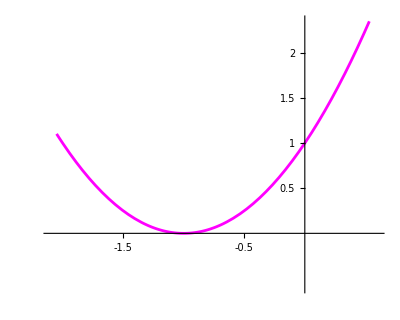

```mathematica
Plot[1+2x+x^2,{x,-2.05,.6},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.1,.6},{-.6,2.35}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8]
```

If we used set of uboxes that are exact or width 1/2, this is what we would like to see as the approximation (in an environment of {1,2} or better, where the endpoints can be represented as exact numbers) is this:

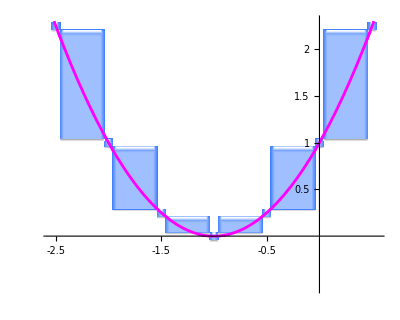

```mathematica
Show[{Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8],
Table[gel2D[i,i,(i+1)^2,(i+1)^2,.04,brightblue,True],{i,-2.5,.5,.5}],
Table[gel2D[i,i+.5,Min[{(i+1)^2,(i+1.5)^2}],Max[{(i+1)^2,(i+1.5)^2}],.04,brightblue,True],{i,-2.5,0,.5}],
Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8]
}]
```

Instead, two of the ubounds will produce unnecessarily loose bounds, close to the root, shown in amber below:

```mathematica
setenv[{1,2}]
set=uboxlist[{OverHat[-2.5],OverHat[0.5]},-1];
Table[ubtogint[{OverHat[1]}⊕{set_⟦i⟧}⊗({OverHat[2]}⊕{set_⟦i⟧})]_⟦1⟧,{i,1,Length[set]}]
```

{{9/4,9/4},{1,9/4},{1,1},{0,1},{1/4,1/4},{-1/2,1/2},{0,0},{-1/2,1/2},{1/4,1/4},{0,1},{1,1},{1,9/4},{9/4,9/4}}

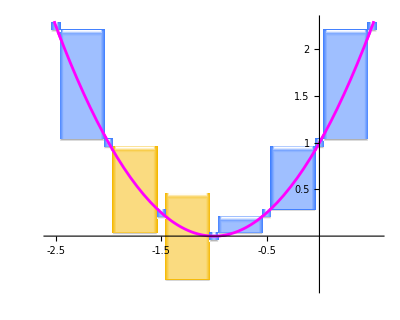

```mathematica
Show[{Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8],
gel2D[-2.5,-2,1,2.25,.04,brightblue,True],
gel2D[-2,-1.5,0,1,.04,cautionamber,True],
gel2D[-1.5,-1,-.5,.5,.04,cautionamber,True],
Table[gel2D[i,i,(i+1)^2,(i+1)^2,.04,brightblue,True],{i,-2.5,.5,.5}],
Table[gel2D[i,i+.5,(i+1)^2,(i+1.5)^2,.04,brightblue,True],{i,-1,0,.5}],
Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8]
}]
```

This is particularly annoying when looking for the roots, solutions to x^2+2x+1=0. The answer should be exact –1, but according to the above graph, it will be the ubound representing (-1.5,1]. Using finer detail (more uboxes) and higher precision reduces the amount of knowledge loss and moves the sloppy calculation much closer to –1, but does not eliminate it. The problem occurs in all polynomials of degree two and higher, since x occurs multiple times in the expression. Generally speaking, the higher the degree of the polynomial, the worse knowledge loss occurs. And the place where it is worst is right near the roots of the polynomial.

This is not merely annoying but downright exasperating to engineers trying to solve control problems. Control theory says that a linear system is stable if all the roots of a certain polynomial are strictly in the left half of the complex plane. That is, their real parts are strictly less than zero. However, the values of x are never known precisely in real world systems, and using an interval for x instead of a point value smears the roots out so badly that you cannot tell whether the answer is yes or no to “Is the system I just designed stable?” The coefficients are generally not exact numbers either, but they only occur once in each evaluation of the polynomial, so they cause no more bound expansion than they are supposed to. The big problem is all the x values being treated as independent ranges, when they are not independent at all.

Polynomials are far too useful to settle for this kind of knowledge loss. A unum environment should include a polynomial routine that provides a tightest-possible evaluation, and the user simply submits the coefficients instead of having to figure out how or why it works.

The author was surprised to discover how long this problem has been in existence; at least sixty years, since the invention of interval arithmetic by Ramon Moore. IBM tried to deal with the problem using an iterative package called ACRITH that alleviated but did not eliminate the error. Occasionally a paper or PhD thesis comes out that shows a way to reduce the error by 25% or so, by trying all possible combinations of operation reorderings. Sort of an “our technique sucks less” approach, chipping away at the problem. Perhaps the reason the problem has not been previously cracked is that people are using floats or traditional intervals, instead of a representation like unums that is careful about open-closed endpoints. In any case, the general approach for evaluating polynomials without any knowledge loss is presented here for the first time.

Start with the general quadratic, so the algebra is easier to read. The equation a+b x+c x^2 can always be rearranged as follows, for a real number x_0:

a+b x+c x^2=(a+b x_0+c x_0)+(b+2c x_0)(x-x_0)+c (x-x_0)^2

In other words, a quadratic equation in x can be written as a quadratic equation in x_0. The x and (x-x_0) values are shown in purple above to make it a bit easier to see that the right hand side is also a quadratic equation. This can be done for any degree polynomial. One way to do it is to replace x on the left with ((x-x_0)+x_0) and expand the result, preserving the grouping of (x-x_0). (An effort is being made to steer clear of calculus and stick to high school algebra here, but calculus offers a different way to think about this: a Taylor series about x_0 with a finite number of terms.)

Notice that the new coefficients each use a, b, and c at most once. That means they can be computed without knowledge loss. If a, b, and c are all exact unums, the new coefficients can be computed perfectly in the exact layer of the computer.

So what good is this type of transformation?

If x can be represented exactly, then it evaluates perfectly because there is not dependency problem. If it is an inexact unum, then it is flanked by exact unums that make excellent choices for x_0. The following graphs show why:

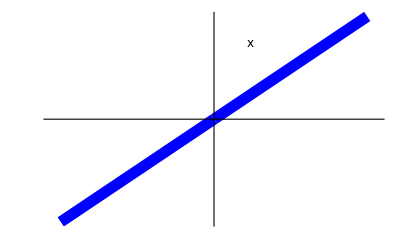
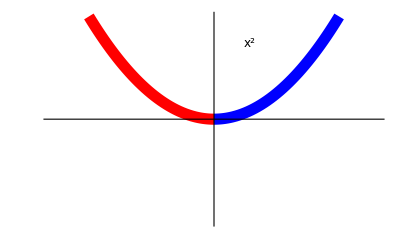
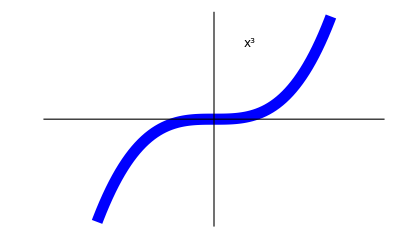
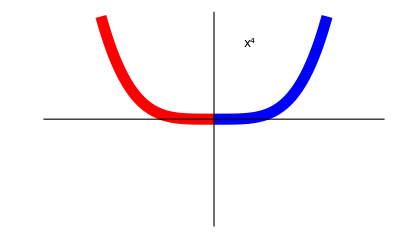
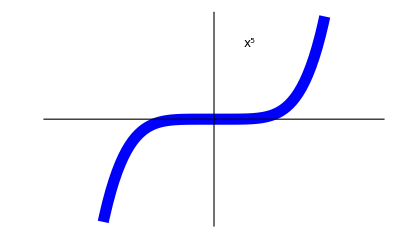
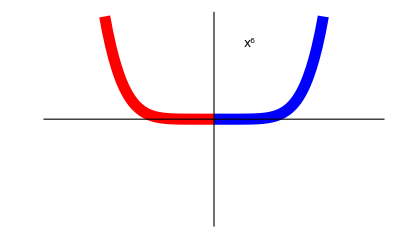
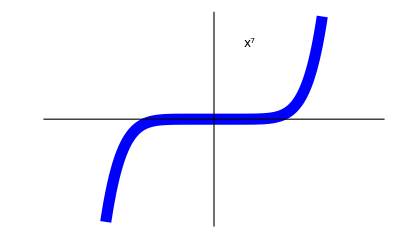
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Blue: power function preserves min-max ordering
Red: power function reverses min-max ordering

```mathematica
Column[{Row[Table[Show[{Plot[x^n,{x,0,1.5},Ticks->False,PlotStyle->{Blue,Thickness[.02]},PlotRange->{{-1.6,1.6},{-1.5,1.5}}],Plot[x^n,{x,-1.5,0},Ticks->False,PlotStyle->{If[EvenQ[n],Red,Blue],Thickness[.02]},PlotRange->{{-1.6,1.6},{-1.5,1.5}}],Graphics[Inset[Style[("x")^n,"Text",12],{.35,1.1}]]}],{n,1,7}],Spacer[6]],
Style["\nBlue: power function preserves min-max ordering","Text"],
Style["Red: power function reverses min-max ordering","Text"]},Alignment->{Center,Center},Spacings->1]
```

The odd powers preserve ordering of a range of values. They are monotone increasing, everywhere. The even powers are monotone increasing for positive values, but monotone decreasing for negative values. That makes it easy to eliminate the dependency problem if all the terms in a sum slope in the same direction. You just evaluate the endpoints, and reverse the result if all the terms were sloping down.

There is a similar set of rules for negative powers of x:

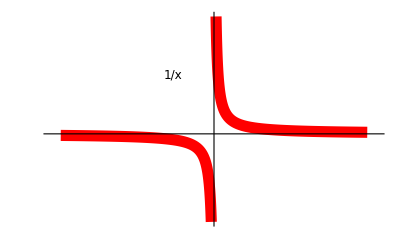
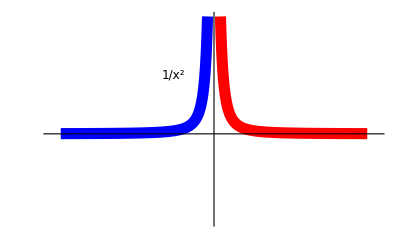
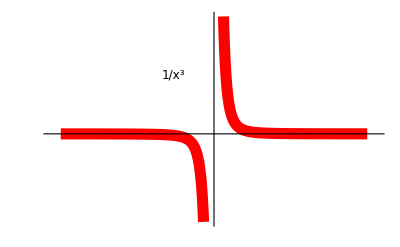
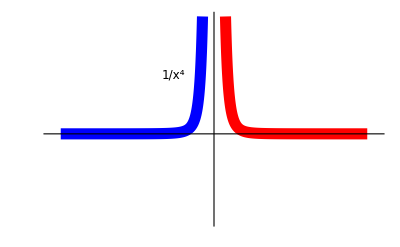
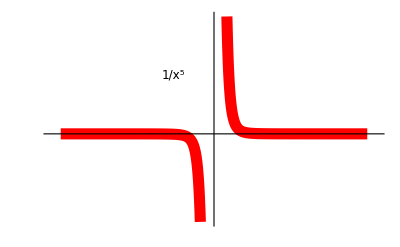
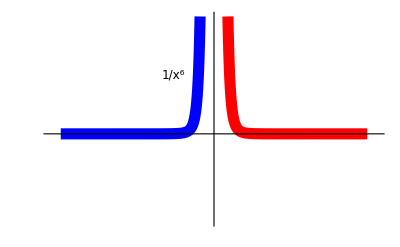
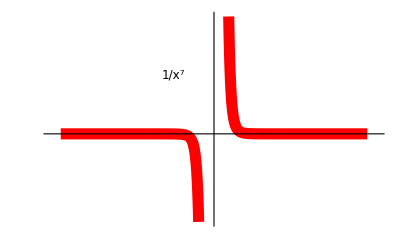
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

Blue: power function preserves min-max ordering
Red: power function reverses min-max ordering

```mathematica
Column[{Row[Table[Show[{Plot[x^n,{x,0,7.5},Ticks->False,PlotStyle->{Red,Thickness[.02]},PlotRange->{{-8,8},{-7.5,10}}],Plot[x^n,{x,-7.5,0},Ticks->False,PlotStyle->{If[OddQ[n],Red,Blue],Thickness[.02]},PlotRange->{{-8,8},{-7.5,10}}],Graphics[Inset[Style[("x")^n,"Text",12],{-2,5}]]}],{n,-1,-7,-1}],Spacer[6]],
Style["\nBlue: power function preserves min-max ordering","Text"],
Style["Red: power function reverses min-max ordering","Text"]},Alignment->{Center,Center},Spacings->1]
```

Taking a reciprocal reverses an inequality. That is, x<y implies 1/x>1/y if x and y are both negative or both strictly positive. But back to polynomials for now.

If x_0 happens to be a root of the polynomial, and the open interval next to x_0 has terms that are all sloping up or all sloping down, then the value of the polynomial on the open interval is just the polynomial of each endpoint, in reverse order if sloping down. If the slopes are inconsistent but an evaluation is within the range of the smallest possible ULP, then the calculation is done. If the slopes are inconsistent and the evaluation is still wider than a single ULP, the open interval is split and the midpoint becomes the new x_0, testing left and right. Splitting continues until both sides either have consistent slopes, or evaluate to a range smaller than the smallest ULP of the environment. The process always eventually arrives at a tight bound if a, b, and c are finite values. (Infinite values can be dispensed with right away, but who wants to use polynomials with unbounded coefficients?)

The newquad[a,b,c,x_0] function gives the new constant, linear, and quadratic coefficients:

```mathematica
newquad[a_,b_,c_,x0_]:={a+b x0+c x0^2,b+2c x0,c}
```

Try the formula for the example quadratic, using x_0=-2:

```mathematica
newquad[1,2,1,-2]
```

{1,-2,1}

That says we can rewrite the equation as

1+2 x+ x^2=1+(-2)(x+2)+(x+2)^2

The slopes are inconsistent in the range (-2,-1.5), just to the right of –2. Try using the right endpoint as x_0 instead, and looking left (which means x^2 is sloping down):

```mathematica
newquad[1,2,1,-1.5]
```

{0.25,-1.,1}

The quadratic can be rewritten as

1+2 x+ x^2=0.25+(-1)(x+1.5)+(x+1.5)^2

This time, the slopes are consistent. The linear term slopes down, and the quadratic term slopes down. So the polynomial evaluates to (0.25+(-1)(-2+1.5)+(-2+1.5)^2=1 on the left, and just the constant term 0.25 on the right, and both endpoints are open, so the tight bound is (0.25,1) as shown in the ideal graph that began this chapter. In this case there was no need to split the range for x, since we found an endpoint that gave us consistent slopes. If the slopes are not consistent, it means there is an extremum somewhere in the range, and the subdivision homes in on it until evaluates to something less than the minimum ULP size wide.

Perhaps one reason this approach does not seem to appear in the literature for interval arithmetic is that traditional intervals start out with a signficant misrepresentation of the answer even in their ideal case:

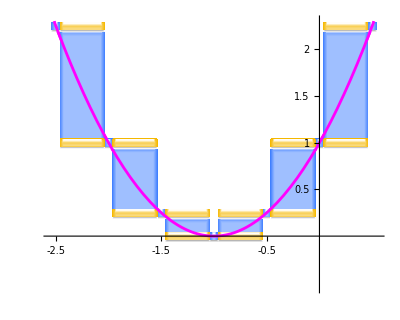

```mathematica
Show[{Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8],
Table[gel2D[i,i,(i+1)^2,(i+1)^2,.04,brightblue,True],{i,-2.5,.5,.5}],
Table[gel2D[i,i+.5,Min[{(i+1)^2,(i+1.5)^2}],Max[{(i+1)^2,(i+1.5)^2}],.04,brightblue,True],{i,-2.5,0,.5}],
Table[gel2D[i,i+.5,(i+1)^2,(i+1)^2,.04,cautionamber,True],{i,-2.5,0,.5}],
Table[gel2D[i,i+.5,(i+1.5)^2,(i+1.5)^2,.04,cautionamber,True],{i,-2.5,0,.5}],
Plot[1+2x+x^2,{x,-2.55,.55},PlotStyle->{Magenta,Thickness[.005]},PlotRange->{{-2.55,.55},{-.55,2.3}},AxesStyle->"Text",Ticks->{{-2.5,-2,-1.5,-1,-.5,.5},{0.5,1,1.5,2}},AspectRatio->.8]
}]
```

The distinction between “greater than” and “greater than or equal” is ignored by traditional intervals, so the entire range from –1.5 to –0.5 looks like a root. Of course, traditional intervals use single or double precision IEEE floats as endpoints, but that means a problem in double precision like “Where is 10^-300 x^2 equal to zero?” gets the spectacularly useless answer of a huge range, from about -10^138 to 10^138 where the calculation “equals” zero. No it doesn’t. In a unum environment, no matter how low the precision, the answer “When x = 0, exactly” is quickly returned since the arithmetic knows that a strictly positive number times a strictly positive numbers is a strictly positive number, even in Warlpiri math.

Time to build the universal quadratic evaluator, as a practice case for the general polynomial. Do it in the exact layer using gints, as usual. It takes a set of three coefficients in coeffsg and an argument xg.

```mathematica
quadg[coeffsg_/;Length[coeffsg]==3∧gintQ[coeffsg_⟦1⟧]∧gintQ[coeffsg_⟦2⟧]∧gintQ[coeffsg_⟦3⟧],xg_/;gintQ[xg]]:=Module[{ag=coeffsg_⟦1⟧,bg=coeffsg_⟦2⟧,cg=coeffsg_⟦3⟧},Which[
(* Dispense with any NaN values first. *)
Or[Table[coeffsg_⟦i,j⟧===NaN,{i,1,3},{j,1,2}]_⟦1⟧]∨xg_⟦1,1⟧===NaN∨xg_⟦1,2⟧===NaN,{{NaN, NaN}, {open, open}},
]
```

```mathematica
Or[Table[x^2==9,{x,0,4}]_⟦1⟧]
```

False

```mathematica
Normal[Series[c x^2+b x+a,{x,x0,4}]]
```

a+c (x-x0)^2+b x0+c x0^2+(x-x0) (b+2 c x0)

```mathematica
polyg[g_/;gQ[g],coeffg_List]:=Module[{ghi,glo,bhi,blo,flipflag,gpower,gL,gR,i,negflag,pL,pR,sL,sR,tg,n1=Length[coeffg]},
Which[
n1==0,{{NaN,NaN},{open,open}},(* No coefficients, no result *)
n1==1∨g=={{0,0},{closed,closed}},coeffg_⟦1⟧, (* No powers to deal with *)
n1==2,plusg[coeffg_⟦1⟧,timesg[coeffg_⟦2⟧,g]], (* Linear. No dependency. *)
True,
{{glo,ghi},{blo,bhi}}=g;
(* Initialize the sum to the c1 + c2*x, left and right separately. *)
tg=plusg[timesg[coeffg_⟦2⟧,g],coeffg_⟦1⟧];
negflag=(ghi<0∨ghi==0∧bhi);
{sL,sR}={{{tg_⟦1,1⟧},{tg_⟦2,1⟧}},{{tg_⟦1,2⟧},{tg_⟦2,2⟧}}};
For[i=3,i≤n1,i++,
flipflag=negflag⊻OddQ[i];
gpower={{glo^(i-1),ghi^(i-1)},{blo,bhi}};
tg=timesg[coeffg_⟦i⟧,If[flipflag,Reverse[gpower],gpower]];
If[flipflag,tg=Reverse[tg]];
{sL,sR}={{{tg_⟦1,1⟧},{tg_⟦2,1⟧}},{{tg_⟦1,2⟧},{tg_⟦2,2⟧}}};

{{sL_⟦1,1⟧,sR_⟦1,1⟧},{sL_⟦2,1⟧,sR_⟦2,1⟧}}]]
```

Here is a generator of a unum test set. Change the environment as desired. Changing j<2^(esize[i]+fsize[i]+1) to j<2^(esize[i]+fsize[i]) gives only nonnegative unums. This has a filter to stop NaN values from getting into the test set, but sometimes those need to be tested also.

```mathematica
n0=n1=n2=n3=0;
setenv[{3,0}]
set={};
Module[{sp,u,ue,uf},
For[i=0,i<2^utagsize,i++,
For[j=0,j<2^(esize[i]+fsize[i]+1),j++,
u=2^utagsize j+i;
(*If[u≠qNaNu∧u≠sNaNu,*)
If[exQ[u]∧g2u[u2g[u]]==={u},
AppendTo[set,u];Print[view[u]," ", hidden[u]," ",frac[u]];f=hidden[u]*2+frac[u];
Which[f==0,n0=n0+1,
f==1,n1=n1+1,
f==2,n2=n2+1,
True,n3=n3+1]]
]
]
];
Length[set]
```

1023

```mathematica
n0
n1
n2
n3
```

1

16

496

510

```mathematica
Table[2*hidden[set_⟦i⟧]+frac[set_⟦i⟧],{i,1,Length[set]}]
```

{0,1,2,3,1,2,3,1,3,2,3,1,3,2,3}

```mathematica
n=0;
For[i=1,i≤Length[set],i++,
For[j=1,j≤Length[set],j++,
w=set_⟦i⟧⊙set_⟦j⟧;
(*Print[view[w]];
*)If[exQ[w_⟦1⟧],n=n+1];]];
Print["Number of exact quotients: ", n]
```

Number of exact quotients: 142

```mathematica
142/225.
```

0.631111

```mathematica
For[i=1,i≤Length[set],i++,
For[j=1,j≤Length[set],j++,
Print[view[set_⟦i⟧]," < ",view[set_⟦j⟧],"?  ",ltuQ[{set_⟦i⟧},{set_⟦j⟧}]]]]
```

```mathematica
Grid[Table[If[j==0,view[set_⟦i⟧],If[nnequQ[{set_⟦i⟧},{set_⟦j⟧}],"T","F"]],{i,1,Length[set]},{j,0,Length[set]}]]
```

0 | T | F | F | F | T | F | F | F | F | F | F | F | F | F | F | F
1 | F | T | F | F | F | F | F | F | F | F | F | F | F | F | F | F
2 | F | F | T | F | F | F | F | F | F | F | F | F | F | F | F | F
∞ | F | F | F | T | F | F | F | F | F | F | F | F | F | F | F | F
0 | T | F | F | F | T | F | F | F | F | F | F | F | F | F | F | F
–1 | F | F | F | F | F | T | F | F | F | F | F | F | F | F | F | F
–2 | F | F | F | F | F | F | T | F | F | F | F | F | F | F | F | F
–∞ | F | F | F | F | F | F | F | T | F | F | F | F | F | F | F | F
(0, 1) | F | F | F | F | F | F | F | F | T | F | F | F | F | F | F | F
(1, 2) | F | F | F | F | F | F | F | F | F | T | F | F | F | F | F | F
(2, ∞) | F | F | F | F | F | F | F | F | F | F | T | F | F | F | F | F
NaN | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F
(–1, 0) | F | F | F | F | F | F | F | F | F | F | F | F | T | F | F | F
(–2, –1) | F | F | F | F | F | F | F | F | F | F | F | F | F | T | F | F
(–∞, –2) | F | F | F | F | F | F | F | F | F | F | F | F | F | F | T | F
NaN | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F | F

```mathematica
Grid[polyg[u2g[set_⟦1⟧],{cg1,cg2,cg1}],Frame->True]
```

2 | 4
False | True

```mathematica
For[i=1,i<Length[set],i++,
Print[view[set_⟦i⟧],"×",view[cg2]," + ",view[cg1]," =  ",Grid[polyg[u2g[set_⟦i⟧],{cg1,cg2,cg1}],Frame->True]]]
```

```mathematica
setenv[{0,0}]
```

```mathematica
badquad[{xmin_,xmax_},a_,b_,c_]:=(a+b Interval[{xmin,xmax}]+c Interval[{xmin,xmax}]^2)_⟦1⟧
```

```mathematica
badquad[{-1,-1/2},-2,-2,-2]
```

{-3,-1/2}

```mathematica
badquadg[xg_,ag_,bg_,cg_]:=plusgint[plusgint[ag,timesgint[bg,xg]],timesgint[cg,squaregint[xg]]]
```

```mathematica
ug={{-1, 0}, {open, open}};ag=bg=cg={{-2, -2}, {closed, closed}};TableForm[badquadg[ug,ag,bg,cg]]
```

-∞ | 0
True | True

```mathematica
betterquadg[ug_,ag_,bg_,cg_]:=Module[{uglo=ug_⟦1,1⟧,ughi=ug_⟦1,2⟧,qg1,qg2,qg3,gm},Which[
uglo===NaN∨ughi===NaN,{{NaN,NaN},{open,open}},
uglo==ughi,(* If exact, safe to use the naive formula. *)
(* Else get the exact values at the endpoints. *)
qg1=badquadg[{{uglo,uglo},{closed,closed}}];
qg3=badquadg[{{ughi,ughi},{closed,closed}}];
qg1==qg3,(* We have a tie. Extremum at midpoint.*)
gm=(uglo+ughi)/2;
gq2=badquadg[{{gm,gm},{closed,closed}}];
```

```mathematica
badquadg[
```

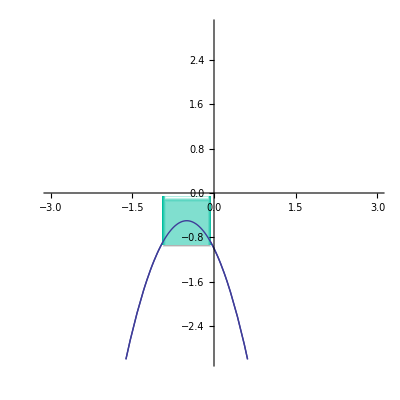

```mathematica
Show[{Plot[-1+(-2)x+(-2)x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],gel2D[-1,0,-1,0,.0625,gogreen,True],Plot[-1+(-2)x+(-2)x^2,{x,-3,3},PlotRange->{{-3,3},{-3,3}}]}]
```

One x_0 endpoint is zero, so that test is easy. b is negative, c is negative but so is x, so contradiction. Dumb evaluation is more than one ULP width:

```mathematica
ug={{-1, 0}, {open, open}};ag={{-1, -1}, {closed, closed}};bg=cg={{-2, -2}, {closed, closed}};
```

```mathematica
badquadg[ug,ag,bg,cg]
```

{{-∞,0},{True,True}}

Look at left endpoint to see if things are any better:

```mathematica
newquad[-1,-2,-2,-1]
```

{-1,2,-2}

So the equation is the same as -1+2(x+1)-2(x+1)^2. All values to the right, but b and c are opposite, so no good. Try it anyway, though it is probably the identical computation to before.

```mathematica
badquadg[{{0, 1}, {open, open}},{{-1, -1}, {closed, closed}},{{2, 2}, {closed, closed}},{{-2, -2}, {closed, closed}}]
```

{{-∞,1},{True,True}}

It’s not identical. It’s worse!

So split the range and use the midpoint as the new x_0.

```mathematica
xLg={{-1, -1/2}, {open, open}};x0g={{-1/2, -1/2}, {closed, closed}};xRg={{-1/2, 0}, {open, open}};
newquad[-1,-2,-2,-1/2]
```

{-1/2,0,-2}

That nailed it, coincidentally; we cannot expect to luck out and land on an extremum exactly very often. The zero value for b says the answer is tight, and is the ubound that unites the three values:

```mathematica
badquadg[{{-1/2, 0}, {open, open}},{{-1/2, -1/2}, {closed, closed}},{{0, 0}, {closed, closed}},{{-2, -2}, {closed, closed}}]
badquadg[{{0, 0}, {closed, closed}},{{-1/2, -1/2}, {closed, closed}},{{0, 0}, {closed, closed}},{{-2, -2}, {closed, closed}}]
badquadg[{{0, 1/2}, {open, open}},{{-1/2, -1/2}, {closed, closed}},{{0, 0}, {closed, closed}},{{-2, -2}, {closed, closed}}]
```

{{-3/2,-1/2},{True,True}}

{{-1/2,-1/2},{False,False}}

{{-3/2,-1/2},{True,True}}

That does not work because it fails to do a Reverse on the values sloping down. What we actually need is

```mathematica
-1/2+{-1/2,0}*{0,0}+Reverse[Reverse[{-1/2,0}^2(-2)]]
```

{-1,-1/2}

```mathematica
Module[{gi,gj},
For[i=1,i<Length[set],i++,
gi=utogint[set_⟦i⟧];
For[j=1,j<Length[set],j++,
gj=utogint[set_⟦j⟧];
Print[viewg[gi], " timesposleft ",viewg[gj]," = ",timesposleft[{{gi_⟦1,1⟧},{gi_⟦2,1⟧}},{{gj_⟦1,1⟧},{gj_⟦2,1⟧}}]]]]]
```

The following generates pairs of unums for testing that are legitimate ubounds.

```mathematica
Module[{g,i,j},
tests={};
For[i=1,i≤Length[set],i++,
For[j=1,j≤Length[set],j++,
g=ubtogint[{set_⟦i⟧,set_⟦j⟧}];
If[uboundQ[{set_⟦i⟧,set_⟦j⟧}],
(*If[g=!={{NaN,NaN},{open,open}}*)
(*∧utogint[set_⟦j⟧]_⟦1,2⟧==∞∧utogint[set_⟦i⟧]_⟦1,1⟧≥3*)
AppendTo[tests,ginttoub[g]]]]]];
Length[tests]
```

1113

```mathematica
For[i=1,i≤Length[tests],i++,
Print[viewg[tests_⟦i⟧]," has split ",Table[viewg[splitub[tests_⟦i⟧]_⟦j⟧],{j,1,Length[splitub[tests_⟦i⟧]]}]]]
```

$Aborted

```mathematica
For[i=1,i≤Length[tests],i++,
For[j=1,j≤Length[tests],j++,
If[Length[tests_⟦i⟧]==2∧Length[tests_⟦j⟧]==2,u=tests_⟦i⟧⊙tests_⟦j⟧;
Print[viewg[tests_⟦i⟧]," ÷ ",viewg[tests_⟦j⟧]," = ",viewg[u]]]]]
```

$Aborted

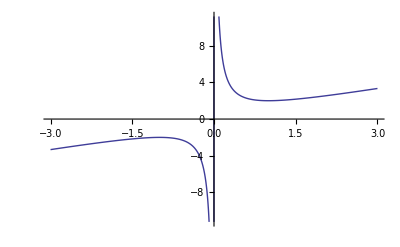

```mathematica
Plot[x+1/x,{x,-3,3}]
```

```mathematica
D[x+1/x,x]
```

1-1/x^2

```mathematica
x=ginttoub[{{3/4, 1}, {open, open}}]
```

{898}

```mathematica
viewg[{OverHat[1]}⊕{OverHat[1]}⊙x]
```

(2, 2.333343505859375)

```mathematica
{1+1/1,.75+1/.75}
```

{2,2.08333}

```mathematica
x=ginttoub[{{1, 5/4}, {open, open}}]
```

{1154}

```mathematica
viewg[{OverHat[1]}⊕{OverHat[1]}⊙x]
```

(1.79998779296875, 2)

```mathematica
{1+1/1,1.25+1/1.25}
```

{2,2.05}

```mathematica
Series[x+1/x,{x,1,8}]
```

2+(x-1)^2-(x-1)^3+(x-1)^4-(x-1)^5+(x-1)^6-(x-1)^7+(x-1)^8+O[x-1]^9

```mathematica
2+∑_(i=1)^∞ (-1/4)^i
```

9/5

```mathematica
2+∑_(i=1)^∞ (1/4)^i
```

7/3

```mathematica
Series[x+1/x,{x,3,8}]
```

10/3+(8 (x-3))/9+1/27 (x-3)^2-1/81 (x-3)^3+1/243 (x-3)^4-1/729 (x-3)^5+(x-3)^6/2187-(x-3)^7/6561+(x-3)^8/19683+O[x-3]^9

```mathematica
∑_(i=1)^∞ y^(2i)/3^(2i)
```

-y^2/(-9+y^2)

```mathematica
1/(-1+9/(x-3)^2)
```

1/(-1+9/(-3+x)^2)

```mathematica
Simplify[%]
```

1/(-1+9/(-3+x)^2)

```mathematica
Simplify[Normal[%]]
```

d+x (c+x (b+a x))

I think I’ve got it. Try both endpoint as x_0 values and evaluate using slope consistency. If the slopes are not consistent and the result intersection is bigger than the smallest ULP, bisect and try each subregion (OK in exact layer to go smaller than the smallest ULP). Stop when the results of a bisection are the same to within the smallest ULP, which means no knowledge loss. Or maybe stop when the evaluation of the ambiguous slope region fits within the evaluation of the oriented slope regions. Looks pretty airtight. 

Suspect that having slopes inconsistent on both sides indicates an extremum inside the range, but proof is not obvious for general polynomials. Easy to prove for quadratics.

Also need a lossless calculation of the bilinear function, (a+b x)/(c+d x). Similar x_0 reasoning should work. Also, could allow negative powers in the polynomial function using same reasoning, which should take care of x+1/x.

```mathematica
Module[{powtableposleft={
{" powg[x,y] left  ","[0","(0","[y","(y","[∞"},
{"[1","[1","[1","[1","[1","(NaN"},
{"(1","[1","(1","(1","(1","[∞"},
{"[x","[1","(1","[x^y","(x^y","[∞"},
{"(x","[1","(1","(x^y","(x^y","[∞"},
{"[∞","(NaN","[∞","[∞","[∞","[∞"}}},
Grid[powtableposleft,Alignment->Center,Spacings->{2,1},Background->{{LightGreen,None},{LightBlue,None}},ItemStyle->{"Text",{{Bold},{Bold}},16},Frame->All]]
```

powg[x,y] left   | [0 | (0 | [y | (y | [∞
[1 | [1 | [1 | [1 | [1 | (NaN
(1 | [1 | (1 | (1 | (1 | [∞
[x | [1 | (1 | [x^y | (x^y | [∞
(x | [1 | (1 | (x^y | (x^y | [∞
[∞ | (NaN | [∞ | [∞ | [∞ | [∞

```mathematica
Module[{timestableposright={
{" powg[x,y] right ","0]","y)","y]","∞)","∞]"},
{"1]","1]","1]","1]","1]","NaN)"},
{"x)","1]","x^y)","x^y)","∞)","∞]"},
{"x]","1]","x^y)","x^y]","∞)","∞]"},
{"∞)","1]","∞)","∞)","∞)","∞]"},
{"∞]","NaN)","∞]","∞]","∞]","∞]"}}},
Grid[timestableposright,Alignment->Center,Spacings->{2,1},Background->{{LightGreen,None},{LightBlue,None}},ItemStyle->{"Text",{{Bold},{Bold}},16},Frame->All]]
```

powg[x,y] right  | 0] | y) | y] | ∞) | ∞]
1] | 1] | 1] | 1] | 1] | NaN)
x) | 1] | x^y) | x^y) | ∞) | ∞]
x] | 1] | x^y) | x^y] | ∞) | ∞]
∞) | 1] | ∞) | ∞) | ∞) | ∞]
∞] | NaN) | ∞] | ∞] | ∞] | ∞]

```mathematica
(* The "left" and "right" multiplication tables for general intervals. *)
powposleft[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{x}, {xb}}=={{1}, {closed}},If[{{y}, {yb}}=={{∞}, {closed}},{{NaN}, {open}},{{1}, {closed}}],
{{y}, {yb}}=={{0}, {closed}},If[{{x}, {xb}}=={{∞}, {closed}},{{NaN}, {open}},{{1}, {closed}}],
{{x}, {xb}}=={{1}, {open}},If[{{y}, {yb}}=={{∞}, {closed}},{{∞}, {closed}},{{1}, {open}}],
{{y}, {yb}}=={{0}, {open}},If[{{x}, {xb}}=={{∞}, {closed}},{{∞}, {closed}},{{1}, {open}}],
{{x}, {xb}}=={{∞}, {closed}}∨{{y}, {yb}}=={{∞}, {closed}},{{∞}, {closed}},
True,{{x^y}, {xb∨yb}}]

powposright[{{x_}, {xb_}},{{y_}, {yb_}}]:=Which[
{{x}, {xb}}=={{∞}, {closed}},If[{{y}, {yb}}=={{0}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{y}, {yb}}=={{∞}, {closed}},If[{{x}, {xb}}=={{1}, {closed}},{{NaN}, {open}},{{∞}, {closed}}],
{{x}, {xb}}=={{∞}, {open}},If[{{y}, {yb}}=={{0}, {closed}},{{1}, {closed}},{{∞}, {open}}],
{{y}, {yb}}=={{∞}, {open}},If[{{x}, {xb}}=={{1}, {closed}},{{1}, {closed}},{{∞}, {open}}],
{{x}, {xb}}=={{1}, {closed}}∨{{y}, {yb}}=={{0}, {closed}},{{1}, {closed}},
True,{{x^y}, {xb∨yb}}]

rec[{{x_}, {xb_}}]:={{Which[x===NaN,NaN,x==0,∞,True,1/x]}, {xb}}
```

```mathematica
powg[{{xlo_, xhi_}, {xlob_, xhib_}},{{ylo_, yhi_}, {ylob_, yhib_}}]:=Module[{powleft,powright,openleft,openright,lcan={},rcan={}},
Which[(* If any value is NaN, the result is also NaN. *)
xlo===NaN∨xhi===NaN∨ylo===NaN∨yhi===NaN,{{NaN, NaN}, {open, open}},
(* Do not allow exact zero to a negative or zero power. *)
(xlo<0∨(xlo==0∧¬xlob))∧(xhi>0∨(xhi==0∧¬xhib))∧(ylo<0∨(ylo==0∧¬ylob)),{{NaN, NaN}, {open, open}},
(* Weird case: complex number of zero magnitude is real. Zero. *)
xhi==-∞∧yhi==-∞∧¬xhib∧¬yhib,{{0, 0}, {closed, closed}},
(* If y is an exact integer, loads of special cases. *)
ylo==yhi∧¬ylob∧¬yhib∧IntegerQ[ylo],
(* Finite nonzero numbers to the power 0 equals 1. *)
Which[ylo==0,If[(0<xlo∨(0==xlo∧xlob))∧(xhi<∞∨(xhi==∞∧xhib))∨(-∞<xlo∨(-∞==xlo∧xlob))∧(xhi<0∨(xhi==0∧xhib)),{{1, 1}, {closed, closed}},{{NaN, NaN}, {open, open}}],
(* Even positive power is like square function; test for zero straddle. *)
EvenQ[ylo]∧ylo>0,Which[
(* Range is strictly negative. Order of endpoints reverses. *)
xhi<0∨xhi==0∧xhib,{lcan,rcan}={powposleft[{{xhi}, {xhib}},{{ylo}, {ylob}}],powposright[{{xlob}, {xlob}},{{ylo}, {ylob}}]},
(* Range is strictly positive. Endpoints preserve ordering. *)
xlo>0∨xlo==0∧xlob,
{lcan,rcan}={powposleft[{{xlo}, {xlob}},{{ylo}, {ylob}}],powposright[{{xhib}, {xhib}},{{ylo}, {ylob}}]},
(* Range straddles zero. Closed zero is lower bound. Larger x^y is upper bound, but beware of ties between open and closed. *)
True,Module[{t1={{xlo^ylo}, {xlob}},t2={{xhi^ylo}, {xhib}},t},t=Which[
t1_⟦1⟧>t2_⟦1⟧,t1,
t1_⟦1⟧<t2_⟦1⟧,t2,
True,{{t1_⟦1⟧}, {xlob∨xhib}}];
{lcan,rcan}={{{0}, {closed}},t}],
{{lcan_⟦1,1⟧, rcan_⟦1,1⟧}, {lcan_⟦2,1⟧, rcan_⟦2,1⟧}}],

(* Even negative power includes +∞ if zero straddle. *)
EvenQ[ylo]∧ylo<0,Which[
(* Range is strictly positive. Order of endpoints reverses. *)
xlo>0∨xlo==0∧xlob,
{lcan,rcan}={powposleft[{{xhi}, {xhib}},{{ylo}, {ylob}}],powposright[{{xlob}, {xlob}},{{ylo}, {ylob}}]},
(* Range is strictly negative. Endpoints preserve ordering. *)
xhi<0∨xhi==0∧xhib,
{lcan,rcan}={powposleft[{{xlo}, {xlob}},{{ylo}, {ylob}}],powposright[{{xhib}, {xhib}},{{ylo}, {ylob}}]},
(* Range straddles zero. Closed infinity is upper bound. smaller x^y is lower bound, but beware of ties between open and closed. *)
True,Module[{t1={{xlo^ylo}, {xlob}},t2={{xhi^ylo}, {xhib}},t},t=Which[
t1_⟦1⟧>t2_⟦1⟧,t2,
t1_⟦1⟧<t2_⟦1⟧,t1,
True,{{t1_⟦1⟧}, {xlob∨xhib}}];
{lcan,rcan}={t,{{∞}, {closed}}};
{{lcan_⟦1,1⟧, rcan_⟦1,1⟧}, {lcan_⟦2,1⟧, rcan_⟦2,1⟧}}]],

(* Else it's an odd integer power. Preserves ordering if positive. *)
ylo>0,{lcan,rcan}={powposleft[{{xlo}, {xlob}},{{ylo}, {ylob}}],powposright[{{xhi}, {xhib}},{{ylo}, {ylob}}]};
{{lcan_⟦1,1⟧, rcan_⟦1,1⟧}, {lcan_⟦2,1⟧, rcan_⟦2,1⟧}},
(* Negative odd power. Reverses ordering. *)
True,{lcan,rcan}={rec[powposleft[{{xhi}, {xhib}},{{-ylo}, {ylob}}]],rec[powposright[{{xlo}, {xlob}},{{-ylo}, {ylob}}]]};
{{lcan_⟦1,1⟧, rcan_⟦1,1⟧}, {lcan_⟦2,1⟧, rcan_⟦2,1⟧}}],
xlo<0,{{NaN, NaN}, {open, open}}, (* Otherwise, negative x not allowed. *)

(* Non-integer exponent, and x is nonnegative. *)
True,
(* Lower left corner is in upper right quadrant, facing uphill: *)
If[xlo≥1∧ylo≥0,lcan=Union[lcan,{powposleft[{{xlo}, {xlob}},{{ylo}, {ylob}}]}]];
(* Upper right corner is in lower left quadrant, facing uphill: *)
If[(xhi<1∨(xhi==1∧xhib))∧(yhi<0∨(yhi==0∧yhib)),lcan=Union[lcan,{powposleft[rec[{{xhi}, {xhib}}],{{-yhi}, {yhib}}]}]];
(* Upper left corner is in upper left quadrant, facing uphill: *)
If[(xlo< 1∨(xlo==1∧¬xlob))∧(yhi>0∨(yhi==0∧¬yhib)),lcan=Union[lcan,{rec[powposright[rec[{{xlo}, {xlob}}],{{yhi}, {yhib}}]]}]];
(* Lower right corner is in lower right quadrant, facing uphill: *)
If[(xhi>1∨(xhi==1∧¬xhib))∧(ylo< 0∨(ylo==0∧¬ylob)),lcan=Union[lcan,{rec[powposright[{{xhi}, {xhib}},{{-ylo}, {ylob}}]]}]];
(* Upper right corner is in upper right quadrant, facing downhill: *)
If[(xhi>1∨(xhi==1∧¬xhib))∧(yhi>0∨(yhi==0∧¬yhib)),rcan=Union[rcan,{powposright[{{xhi}, {xhib}},{{yhi}, {yhib}}]}]];
(* Lower left corner is in lower left quadrant, facing downhill: *)
If[(xlo< 1∨(xlo==1∧¬xlob))∧(ylo< 0∨(ylo==0∧¬ylob)),rcan=Union[rcan,{powposright[rec[{{xlo}, {xlob}}],{{-ylo}, {ylob}}]}]];
(* Lower right corner is in upper left quadrant, facing downhill: *)
If[(xhi<1∨(xhi==1∧xhib))∧ylo≥ 0,rcan=Union[rcan,{rec[powposleft[rec[{{xhi}, {xhib}}],{{ylo}, {ylob}}]]}]];
(* Upper left corner is in lower right quadrant, facing downhill: *)
If[xlo≥1∧(yhi<0∨(yhi==0∧yhib)),rcan=Union[rcan,{rec[powposleft[{{xlo}, {xlob}},{{-yhi}, {yhib}}]]}]];
If[MemberQ[Flatten[lcan],NaN]∨MemberQ[Flatten[rcan],NaN],{{powleft, powright}, {openleft, openright}}={{NaN, NaN}, {open, open}}];
{{powleft, powright}, {openleft, openright}}={{lcan_⟦1,1,1⟧, rcan_⟦-1,1,1⟧}, {lcan_⟦1,2,1⟧, rcan_⟦-1,2,1⟧}};
If[Length[lcan]>1,If[lcan_⟦1,1,1⟧==lcan_⟦2,1,1⟧∧(¬lcan_⟦1,2,1⟧∨¬lcan_⟦2,2,1⟧),openleft=closed]];
If[Length[rcan]>1,If[rcan_⟦-1,1,1⟧==rcan_⟦-2,1,1⟧∧(¬rcan_⟦-1,2,1⟧∨¬rcan_⟦-2,2,1⟧),openright=closed]];
{{powleft, powright}, {openleft, openright}}]]
```

```mathematica
powu[u_/;uQ[u],v_/;uQ[v]]:=Module[{w=g2u[powg[u2g[u],u2g[v]]]},
ubitsmoved+=nbits[u]+nbits[v]+nbits[w];numbersmoved+=3;w]
```

(0, 1) to the power –2 = view[g2u[{{1,ComplexInfinity},{True,True}}]]

```mathematica
{{xlo, xhi}, {xlob, xhib}}={{0, 1}, {open, open}};{{ylo, yhi}, {ylob, yhib}}={{-2, -2}, {closed, closed}};lcan={};rcan={};
```

```mathematica
Module[{t1=xlo^ylo,t2=xhi^ylo,tset},
tset=Sort[{{t1,xlob},{t2,xhib}}];Which[(* See if 0 is in the range *)
(xlo<0∧xhi>0)∨(xlo>0∧xhi<0)∨(xlo==0∧¬xlob)∨(xhi==0∧¬xhib),If[t1==t2,{{t2,∞},{xlob∧xhib,closed}},{{tset_⟦1,1⟧,∞},{tset_⟦1,2⟧,closed}}],
True,Transpose[tset]]]
```

Power::infy: Infinite expression 1/0^2 encountered.

{{1,ComplexInfinity},{True,True}}

```mathematica
powg[{{xlo, xhi}, {xlob, xhib}},{{ylo, yhi}, {ylob, yhib}}]
```

Power::infy: Infinite expression 1/0^2 encountered.

{{1,ComplexInfinity},{True,True}}

```mathematica
lcan=powposleft[{{xhi}, {xhib}},{{ylo}, {ylob}}]
rcan=powposright[{{xlo}, {xlob}},{{ylo}, {ylob}}]
```

{{∞},{False}}

{{∞},{False}}

```mathematica
(xlo<0∨(xlo==0∧¬xlob))∧(xhi>0∨(xhi==0∧¬xhib))∧(ylo<0∨(ylo==0∧¬ylob))
```

False

```mathematica
xhi≥0
```

False

```mathematica
rcan=Union[rcan,{rec[powposleft[rec[{{xhi}, {xhib}}],{{ylo}, {ylob}}]]}]
```

{{{1},{False}}}

```mathematica
{{xhi^ylo, xlo^ylo}, {xhib, xlob}}
```

{{-∞,-∞},{False,False}}

```mathematica
powg[{{81/256, 625/256}, {closed, open}},{{1/4, 1/4}, {closed, closed}}]
```

{{3/4,5/4},{False,True}}

### Power function x^y

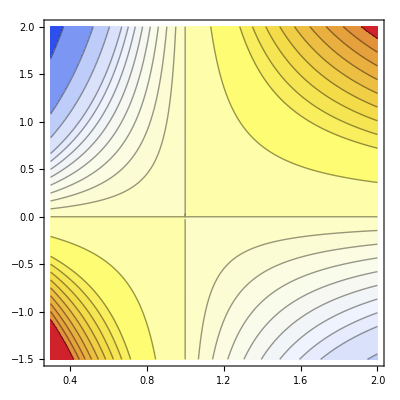

```mathematica
ContourPlot[Log[x^y],{x,.3,2},{y,-1.5,2},Contours->{-2,-1.3,-1,-.8,-.7,-.6,-.5,-.4,-.3,-.2,-.1,0,.25,.5,.6,.7,.8,.9,1,1.1,1.2,1.3},MaxRecursion->4,LabelStyle->Directive["Text"],ColorFunction->ColorData["TemperatureMap"]]
```

```mathematica
setenv[{3,5}]
```

```mathematica
powu[OverHat[0],OverHat[0]]
```

{7}

```mathematica
setenv[{0,0}]
set={};
Module[{sp,u,ue,uf},
For[i=0,i<2^utagsize,i++,
For[j=0,j<2^(esize[i]+fsize[i]+1),j++,
u=2^utagsize j+i;
(*If[u≠qNaNu∧u≠sNaNu,*)
AppendTo[set,u]
]
]
];
Length[set]
```

16

```mathematica
For[i=1,i≤Length[set],i++,
For[j=1,j≤Length[set],j++,
Print[view[set_⟦i⟧]," to the power ",view[set_⟦j⟧]," = ",view[powu[set_⟦i⟧,set_⟦j⟧]]]]]
```

0 to the power 0 = NaN

0 to the power 1 = 0

Which::argct: Which called with 7 arguments.

0 to the power 2 = view[g2u[Which[0<0||(0==0&&False),{lcan$591815,rcan$591815}={powposleft[{{0},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},0>0||(0==0&&False),{lcan$591815,rcan$591815}={powposleft[{{0},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{0^2},{False}},t2$={{0^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$591815,rcan$591815}={{{0},{closed}},t$}],{{lcan$591815⟦1,1⟧,rcan$591815⟦1,1⟧},{lcan$591815⟦2,1⟧,rcan$591815⟦2,1⟧}}]]]

0 to the power ∞ = 0

0 to the power 0 = NaN

0 to the power –1 = NaN

0 to the power –2 = NaN

0 to the power –∞ = NaN

0 to the power (0, 1) = 0

0 to the power (1, 2) = 0

0 to the power (2, ∞) = 0

0 to the power NaN = NaN

0 to the power (–1, 0) = NaN

0 to the power (–2, –1) = NaN

0 to the power (–∞, –2) = NaN

0 to the power NaN = NaN

1 to the power 0 = 1

1 to the power 1 = 1

Which::argct: Which called with 7 arguments.

1 to the power 2 = view[g2u[Which[1<0||(1==0&&False),{lcan$592566,rcan$592566}={powposleft[{{1},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},1>0||(1==0&&False),{lcan$592566,rcan$592566}={powposleft[{{1},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{1^2},{False}},t2$={{1^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$592566,rcan$592566}={{{0},{closed}},t$}],{{lcan$592566⟦1,1⟧,rcan$592566⟦1,1⟧},{lcan$592566⟦2,1⟧,rcan$592566⟦2,1⟧}}]]]

1 to the power ∞ = NaN

1 to the power 0 = 1

1 to the power –1 = 1

1 to the power –2 = view[g2u[{{{1},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

1 to the power –∞ = NaN

1 to the power (0, 1) = 1

1 to the power (1, 2) = 1

1 to the power (2, ∞) = 1

1 to the power NaN = NaN

1 to the power (–1, 0) = 1

1 to the power (–2, –1) = 1

1 to the power (–∞, –2) = 1

1 to the power NaN = NaN

2 to the power 0 = 1

2 to the power 1 = 2

Which::argct: Which called with 7 arguments.

General::stop: Further output of Which :: argct will be suppressed during this calculation.

2 to the power 2 = view[g2u[Which[2<0||(2==0&&False),{lcan$593377,rcan$593377}={powposleft[{{2},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},2>0||(2==0&&False),{lcan$593377,rcan$593377}={powposleft[{{2},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{2^2},{False}},t2$={{2^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$593377,rcan$593377}={{{0},{closed}},t$}],{{lcan$593377⟦1,1⟧,rcan$593377⟦1,1⟧},{lcan$593377⟦2,1⟧,rcan$593377⟦2,1⟧}}]]]

2 to the power ∞ = ∞

2 to the power 0 = 1

2 to the power –1 = (0, 1)

2 to the power –2 = view[g2u[{{{1/4},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

2 to the power –∞ = 0

2 to the power (0, 1) = (1, 2)

2 to the power (1, 2) = (2, ∞)

2 to the power (2, ∞) = (2, ∞)

2 to the power NaN = NaN

2 to the power (–1, 0) = (0, 1)

2 to the power (–2, –1) = (0, 1)

2 to the power (–∞, –2) = (0, 1)

2 to the power NaN = NaN

∞ to the power 0 = NaN

∞ to the power 1 = ∞

∞ to the power 2 = view[g2u[Which[∞<0||(∞==0&&False),{lcan$595019,rcan$595019}={powposleft[{{∞},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},∞>0||(∞==0&&False),{lcan$595019,rcan$595019}={powposleft[{{∞},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{∞^2},{False}},t2$={{∞^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$595019,rcan$595019}={{{0},{closed}},t$}],{{lcan$595019⟦1,1⟧,rcan$595019⟦1,1⟧},{lcan$595019⟦2,1⟧,rcan$595019⟦2,1⟧}}]]]

∞ to the power ∞ = ∞

∞ to the power 0 = NaN

∞ to the power –1 = 0

∞ to the power –2 = view[g2u[{{{∞},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

∞ to the power –∞ = 0

∞ to the power (0, 1) = ∞

∞ to the power (1, 2) = ∞

∞ to the power (2, ∞) = ∞

∞ to the power NaN = NaN

∞ to the power (–1, 0) = 0

∞ to the power (–2, –1) = 0

∞ to the power (–∞, –2) = 0

∞ to the power NaN = NaN

0 to the power 0 = NaN

0 to the power 1 = 0

0 to the power 2 = view[g2u[Which[0<0||(0==0&&False),{lcan$595461,rcan$595461}={powposleft[{{0},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},0>0||(0==0&&False),{lcan$595461,rcan$595461}={powposleft[{{0},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{0^2},{False}},t2$={{0^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$595461,rcan$595461}={{{0},{closed}},t$}],{{lcan$595461⟦1,1⟧,rcan$595461⟦1,1⟧},{lcan$595461⟦2,1⟧,rcan$595461⟦2,1⟧}}]]]

0 to the power ∞ = 0

0 to the power 0 = NaN

0 to the power –1 = NaN

0 to the power –2 = NaN

0 to the power –∞ = NaN

0 to the power (0, 1) = 0

0 to the power (1, 2) = 0

0 to the power (2, ∞) = 0

0 to the power NaN = NaN

0 to the power (–1, 0) = NaN

0 to the power (–2, –1) = NaN

0 to the power (–∞, –2) = NaN

0 to the power NaN = NaN

–1 to the power 0 = 1

–1 to the power 1 = –1

–1 to the power 2 = view[g2u[Which[-1<0||(-1==0&&False),{lcan$595880,rcan$595880}={powposleft[{{-1},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},-1>0||(-1==0&&False),{lcan$595880,rcan$595880}={powposleft[{{-1},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{(-1)^2},{False}},t2$={{(-1)^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$595880,rcan$595880}={{{0},{closed}},t$}],{{lcan$595880⟦1,1⟧,rcan$595880⟦1,1⟧},{lcan$595880⟦2,1⟧,rcan$595880⟦2,1⟧}}]]]

–1 to the power ∞ = NaN

–1 to the power 0 = 1

–1 to the power –1 = –1

–1 to the power –2 = view[g2u[{{{1},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

–1 to the power –∞ = NaN

–1 to the power (0, 1) = NaN

–1 to the power (1, 2) = NaN

–1 to the power (2, ∞) = NaN

–1 to the power NaN = NaN

–1 to the power (–1, 0) = NaN

–1 to the power (–2, –1) = NaN

–1 to the power (–∞, –2) = NaN

–1 to the power NaN = NaN

–2 to the power 0 = 1

–2 to the power 1 = –2

–2 to the power 2 = view[g2u[Which[-2<0||(-2==0&&False),{lcan$596304,rcan$596304}={powposleft[{{-2},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},-2>0||(-2==0&&False),{lcan$596304,rcan$596304}={powposleft[{{-2},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{(-2)^2},{False}},t2$={{(-2)^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$596304,rcan$596304}={{{0},{closed}},t$}],{{lcan$596304⟦1,1⟧,rcan$596304⟦1,1⟧},{lcan$596304⟦2,1⟧,rcan$596304⟦2,1⟧}}]]]

–2 to the power ∞ = NaN

–2 to the power 0 = 1

–2 to the power –1 = (–1, 0)

–2 to the power –2 = view[g2u[{{{1/4},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

–2 to the power –∞ = NaN

–2 to the power (0, 1) = NaN

–2 to the power (1, 2) = NaN

–2 to the power (2, ∞) = NaN

–2 to the power NaN = NaN

–2 to the power (–1, 0) = NaN

–2 to the power (–2, –1) = NaN

–2 to the power (–∞, –2) = NaN

–2 to the power NaN = NaN

–∞ to the power 0 = NaN

–∞ to the power 1 = –∞

–∞ to the power 2 = view[g2u[Which[-∞<0||(-∞==0&&False),{lcan$596711,rcan$596711}={powposleft[{{-∞},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},-∞>0||(-∞==0&&False),{lcan$596711,rcan$596711}={powposleft[{{-∞},{False}},{{2},{False}}],powposright[{{False},{False}},{{2},{False}}]},True,Module[{t1$={{(-∞)^2},{False}},t2$={{(-∞)^2},{False}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{False||False}}];{lcan$596711,rcan$596711}={{{0},{closed}},t$}],{{lcan$596711⟦1,1⟧,rcan$596711⟦1,1⟧},{lcan$596711⟦2,1⟧,rcan$596711⟦2,1⟧}}]]]

–∞ to the power ∞ = NaN

–∞ to the power 0 = NaN

–∞ to the power –1 = 0

–∞ to the power –2 = view[g2u[{{{0},{False}},Which[{{False},{False}}=={{∞},{False}},If[{{-2},{False}}=={{0},{closed}},{{NaN},{open}},{{∞},{closed}}],{{-2},{False}}=={{∞},{closed}},If[{{False},{False}}=={{1},{closed}},{{NaN},{open}},{{∞},{closed}}],{{False},{False}}=={{∞},{open}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{False},{False}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{False},{False}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/False^2},{False||False}}]}]]

–∞ to the power –∞ = 0

–∞ to the power (0, 1) = NaN

–∞ to the power (1, 2) = NaN

–∞ to the power (2, ∞) = NaN

–∞ to the power NaN = NaN

–∞ to the power (–1, 0) = NaN

–∞ to the power (–2, –1) = NaN

–∞ to the power (–∞, –2) = NaN

–∞ to the power NaN = NaN

(0, 1) to the power 0 = 1

(0, 1) to the power 1 = (0, 1)

(0, 1) to the power 2 = view[g2u[Which[1<0||(1==0&&True),{lcan$597258,rcan$597258}={powposleft[{{1},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},0>0||(0==0&&True),{lcan$597258,rcan$597258}={powposleft[{{0},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{0^2},{True}},t2$={{1^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$597258,rcan$597258}={{{0},{closed}},t$}],{{lcan$597258⟦1,1⟧,rcan$597258⟦1,1⟧},{lcan$597258⟦2,1⟧,rcan$597258⟦2,1⟧}}]]]

(0, 1) to the power ∞ = 0

(0, 1) to the power 0 = 1

(0, 1) to the power –1 = (1, ∞)

(0, 1) to the power –2 = view[g2u[{{{1},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(0, 1) to the power –∞ = ∞

(0, 1) to the power (0, 1) = (0, 1)

(0, 1) to the power (1, 2) = (0, 1)

(0, 1) to the power (2, ∞) = (0, 1)

(0, 1) to the power NaN = NaN

(0, 1) to the power (–1, 0) = (1, ∞)

(0, 1) to the power (–2, –1) = (1, ∞)

(0, 1) to the power (–∞, –2) = (1, ∞)

(0, 1) to the power NaN = NaN

(1, 2) to the power 0 = 1

(1, 2) to the power 1 = (1, 2)

(1, 2) to the power 2 = view[g2u[Which[2<0||(2==0&&True),{lcan$599490,rcan$599490}={powposleft[{{2},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},1>0||(1==0&&True),{lcan$599490,rcan$599490}={powposleft[{{1},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{1^2},{True}},t2$={{2^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$599490,rcan$599490}={{{0},{closed}},t$}],{{lcan$599490⟦1,1⟧,rcan$599490⟦1,1⟧},{lcan$599490⟦2,1⟧,rcan$599490⟦2,1⟧}}]]]

(1, 2) to the power ∞ = ∞

(1, 2) to the power 0 = 1

(1, 2) to the power –1 = (0, 1)

(1, 2) to the power –2 = view[g2u[{{{1/4},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(1, 2) to the power –∞ = 0

(1, 2) to the power (0, 1) = (1, 2)

(1, 2) to the power (1, 2) = (1, ∞)

(1, 2) to the power (2, ∞) = (1, ∞)

(1, 2) to the power NaN = NaN

(1, 2) to the power (–1, 0) = (0, 1)

(1, 2) to the power (–2, –1) = (0, 1)

(1, 2) to the power (–∞, –2) = (0, 1)

(1, 2) to the power NaN = NaN

(2, ∞) to the power 0 = 1

(2, ∞) to the power 1 = (2, ∞)

(2, ∞) to the power 2 = view[g2u[Which[∞<0||(∞==0&&True),{lcan$601402,rcan$601402}={powposleft[{{∞},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},2>0||(2==0&&True),{lcan$601402,rcan$601402}={powposleft[{{2},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{2^2},{True}},t2$={{∞^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$601402,rcan$601402}={{{0},{closed}},t$}],{{lcan$601402⟦1,1⟧,rcan$601402⟦1,1⟧},{lcan$601402⟦2,1⟧,rcan$601402⟦2,1⟧}}]]]

(2, ∞) to the power ∞ = ∞

(2, ∞) to the power 0 = 1

(2, ∞) to the power –1 = (0, 1)

(2, ∞) to the power –2 = view[g2u[{{{0},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(2, ∞) to the power –∞ = 0

(2, ∞) to the power (0, 1) = (1, ∞)

(2, ∞) to the power (1, 2) = (2, ∞)

(2, ∞) to the power (2, ∞) = (2, ∞)

(2, ∞) to the power NaN = NaN

(2, ∞) to the power (–1, 0) = (0, 1)

(2, ∞) to the power (–2, –1) = (0, 1)

(2, ∞) to the power (–∞, –2) = (0, 1)

(2, ∞) to the power NaN = NaN

NaN to the power 0 = NaN

NaN to the power 1 = NaN

NaN to the power 2 = NaN

NaN to the power ∞ = NaN

NaN to the power 0 = NaN

NaN to the power –1 = NaN

NaN to the power –2 = NaN

NaN to the power –∞ = NaN

NaN to the power (0, 1) = NaN

NaN to the power (1, 2) = NaN

NaN to the power (2, ∞) = NaN

NaN to the power NaN = NaN

NaN to the power (–1, 0) = NaN

NaN to the power (–2, –1) = NaN

NaN to the power (–∞, –2) = NaN

NaN to the power NaN = NaN

(–1, 0) to the power 0 = 1

(–1, 0) to the power 1 = (–1, 0)

(–1, 0) to the power 2 = view[g2u[Which[0<0||(0==0&&True),{lcan$603857,rcan$603857}={powposleft[{{0},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},-1>0||(-1==0&&True),{lcan$603857,rcan$603857}={powposleft[{{-1},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{(-1)^2},{True}},t2$={{0^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$603857,rcan$603857}={{{0},{closed}},t$}],{{lcan$603857⟦1,1⟧,rcan$603857⟦1,1⟧},{lcan$603857⟦2,1⟧,rcan$603857⟦2,1⟧}}]]]

(–1, 0) to the power ∞ = NaN

(–1, 0) to the power 0 = 1

(–1, 0) to the power –1 = view[g2u[{{∞,-1},{True,True}}]]

(–1, 0) to the power –2 = view[g2u[{{{1},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(–1, 0) to the power –∞ = NaN

(–1, 0) to the power (0, 1) = NaN

(–1, 0) to the power (1, 2) = NaN

(–1, 0) to the power (2, ∞) = NaN

(–1, 0) to the power NaN = NaN

(–1, 0) to the power (–1, 0) = NaN

(–1, 0) to the power (–2, –1) = NaN

(–1, 0) to the power (–∞, –2) = NaN

(–1, 0) to the power NaN = NaN

(–2, –1) to the power 0 = 1

(–2, –1) to the power 1 = (–2, –1)

(–2, –1) to the power 2 = view[g2u[Which[-1<0||(-1==0&&True),{lcan$604855,rcan$604855}={powposleft[{{-1},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},-2>0||(-2==0&&True),{lcan$604855,rcan$604855}={powposleft[{{-2},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{(-2)^2},{True}},t2$={{(-1)^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$604855,rcan$604855}={{{0},{closed}},t$}],{{lcan$604855⟦1,1⟧,rcan$604855⟦1,1⟧},{lcan$604855⟦2,1⟧,rcan$604855⟦2,1⟧}}]]]

(–2, –1) to the power ∞ = NaN

(–2, –1) to the power 0 = 1

(–2, –1) to the power –1 = (–1, 0)

(–2, –1) to the power –2 = view[g2u[{{{1/4},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(–2, –1) to the power –∞ = NaN

(–2, –1) to the power (0, 1) = NaN

(–2, –1) to the power (1, 2) = NaN

(–2, –1) to the power (2, ∞) = NaN

(–2, –1) to the power NaN = NaN

(–2, –1) to the power (–1, 0) = NaN

(–2, –1) to the power (–2, –1) = NaN

(–2, –1) to the power (–∞, –2) = NaN

(–2, –1) to the power NaN = NaN

(–∞, –2) to the power 0 = 1

(–∞, –2) to the power 1 = (–∞, –2)

(–∞, –2) to the power 2 = view[g2u[Which[-2<0||(-2==0&&True),{lcan$606435,rcan$606435}={powposleft[{{-2},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},-∞>0||(-∞==0&&True),{lcan$606435,rcan$606435}={powposleft[{{-∞},{True}},{{2},{False}}],powposright[{{True},{True}},{{2},{False}}]},True,Module[{t1$={{(-∞)^2},{True}},t2$={{(-2)^2},{True}},t$},t$=Which[t1$⟦1⟧>t2$⟦1⟧,t1$,t1$⟦1⟧<t2$⟦1⟧,t2$,True,{{t1$⟦1⟧},{True||True}}];{lcan$606435,rcan$606435}={{{0},{closed}},t$}],{{lcan$606435⟦1,1⟧,rcan$606435⟦1,1⟧},{lcan$606435⟦2,1⟧,rcan$606435⟦2,1⟧}}]]]

(–∞, –2) to the power ∞ = NaN

(–∞, –2) to the power 0 = 1

(–∞, –2) to the power –1 = (–1, 0)

(–∞, –2) to the power –2 = view[g2u[{{{0},{True}},Which[{{True},{True}}=={{∞},{True}},If[{{-2},{False}}=={{0},{closed}},{{1},{closed}},{{∞},{open}}],{{-2},{False}}=={{∞},{open}},If[{{True},{True}}=={{1},{closed}},{{1},{closed}},{{∞},{open}}],{{True},{True}}=={{1},{closed}}||{{-2},{False}}=={{0},{closed}},{{1},{closed}},True,{{1/True^2},{True||False}}]}]]

(–∞, –2) to the power –∞ = NaN

(–∞, –2) to the power (0, 1) = NaN

(–∞, –2) to the power (1, 2) = NaN

(–∞, –2) to the power (2, ∞) = NaN

(–∞, –2) to the power NaN = NaN

(–∞, –2) to the power (–1, 0) = NaN

(–∞, –2) to the power (–2, –1) = NaN

(–∞, –2) to the power (–∞, –2) = NaN

(–∞, –2) to the power NaN = NaN

NaN to the power 0 = NaN

NaN to the power 1 = NaN

NaN to the power 2 = NaN

NaN to the power ∞ = NaN

NaN to the power 0 = NaN

NaN to the power –1 = NaN

NaN to the power –2 = NaN

NaN to the power –∞ = NaN

NaN to the power (0, 1) = NaN

NaN to the power (1, 2) = NaN

NaN to the power (2, ∞) = NaN

NaN to the power NaN = NaN

NaN to the power (–1, 0) = NaN

NaN to the power (–2, –1) = NaN

NaN to the power (–∞, –2) = NaN

NaN to the power NaN = NaN